```mathematica
pivots[A_]:=Flatten[FirstPosition[1]/@Transpose[A]]
```

```mathematica
pMatrix[n_]:=Table[Which[i==2&&j==1||i==1&&j==2,-1/2,i==j&&i>2,1,True,0],{i, n},{j,n}]
```

```mathematica
gramMatrix[W_]:=Simplify[Transpose[W].pMatrix[Length[W]].W]
```

```mathematica
linearRelationsMatrix[G_]:=RowReduce[G][[1;;MatrixRank[G]]]//Transpose
```

```mathematica
linearRelations[L_]:=Select[Table[Equal[Subscript[b, i],L[[i]].Table[Subscript[b, i],{i,pivots[L]}]],{i,Length[L]}],Not[BooleanQ[#]]&]
```

```mathematica
linearRelationsFromW=linearRelations@*linearRelationsMatrix@*gramMatrix;
```

```mathematica
inverseLinearRelations[G_]:=Table[If[i==#,1,0],{i,Length[G[[1]]]}]&/@Flatten[FirstPosition[#,1]&/@(RowReduce[G]//Select[Not[AllTrue[#,#==0&]]&])]
```

```mathematica
quadraticFormMatrix[G_,L_]:=Inverse[Table[G[[i, j]],{i,pivots[L]},{j,pivots[L]}]]
```

```mathematica
quadraticForm[Q_,L_]:=Module[{v=Table[Subscript[b, i],{i,pivots[L]}]},Simplify[v.Q.v==0]]
```

```mathematica
quadform[W_]:=Module[{G=gramMatrix[W]},Module[{L=linearRelationsMatrix[G]},quadraticForm[quadraticFormMatrix[G,L],L]]]
```

```mathematica
quadformFromG[G_]:=Module[{L=linearRelationsMatrix[G]},quadraticForm[quadraticFormMatrix[G,L],L]]
```

```mathematica
graphFromG[G_]:=PlanarGraph[AdjacencyGraph[If[#==-1,1,0]&/@#&/@G,VertexLabels->"Name"]]
```

```mathematica
nextCandidate[s_,t_,adj_]:=Block[{length,pos},length=Length[adj];
pos=Mod[Position[adj,s][[1,1]]+1,length,1];
{t,adj[[pos]]}];
```

```mathematica
FindFace[g_?PlanarGraphQ]:=Block[{emb},emb=GraphEmbedding[g,"PlanarEmbedding"];
FindFace[g,emb]];

FindFace[g_?PlanarGraphQ,emb_]:=Block[{m,orderings,pAdj,rightF,s,t,initial,face},m=AdjacencyMatrix[g];
Table[pAdj[v]=SortBy[Pick[VertexList[g],m[[v]],1],ArcTan@@(emb[[v]]-emb[[#]])&],{v,VertexList[g]}];
rightF[_]:=False;
Reap[Table[If[!rightF[e],s=e[[1]];
t=e[[2]];
initial=s;
face={s};
While[t=!=initial,rightF[UndirectedEdge[s,t]]=True;
{s,t}=nextCandidate[s,t,pAdj[t]];
face=Join[face,{s}];];
Sow[face];],{e,EdgeList[g]}]][[2,1]]]
```

```mathematica
findGenerators[faces_,vertices_,G_]:=Table[Block[{face,otherVertex,verticesOnFace,allVertices,Gp,P,Gnew,L,Q,Qform,sol1,sol2,sols,coeff,coeffTable,small,Li,P2},
face=faces[[i]];
verticesOnFace=Sort[RandomSample[face,3]];
otherVertex=RandomChoice[Select[vertices,Not[MemberQ[face,#]]&]];
allVertices=Append[verticesOnFace,otherVertex];
P=Transpose[IdentityMatrix[Length[vertices]][[#]]&/@DeleteDuplicates[Join[allVertices,vertices]]];
Gnew=Transpose[P].G.P;
L=linearRelationsMatrix[Gnew];
Gp=Table[G[[i,j]],{i,allVertices},{j,allVertices}];
Q=Inverse[Gp];
Qform=(#.Q.#&[Table[Subscript[b, j],{j,allVertices}]])==0;
sols=Expand[FullSimplify[Total[#[[1]][[2]]&/@Solve[Qform,Subscript[b, otherVertex]]]]];
coeff=Table[sols/.Table[Subscript[b, i]->If[i==curr,1,0],{i,allVertices}],{curr,allVertices}];
small=IdentityMatrix[Length[allVertices]];
small[[-1]]=Table[If[j==4,-1,If[MemberQ[verticesOnFace,allVertices[[j]]],coeff[[j]],0]],{j,Length[allVertices]}];
Li=Table[Table[If[j==k,1,0],{j,Length[vertices]}],{k,allVertices}];
P2=Table[If[j==k,1,0],{j,Length[vertices]},{k,DeleteDuplicates[Join[allVertices,vertices]]}];
P2.L.small.Li
],{i,Length[faces]}]
```

```mathematica
findGeneratorsN[faces_,vertices_,G_]:=Table[Block[{face,otherVertex,verticesOnFace,allVertices,Gp,P,Gnew,L,Q,Qform,sol1,sol2,sols,coeff,coeffTable,small,Li,P2},
face=faces⟦i⟧;
verticesOnFace=Sort[RandomSample[face,3]];
otherVertex=RandomChoice[Select[vertices,Not[MemberQ[face,#]]&]];
allVertices=Append[verticesOnFace,otherVertex];
P=Transpose[IdentityMatrix[Length[vertices]]⟦#⟧&/@DeleteDuplicates[Join[allVertices,vertices]]];
Gnew=Transpose[P].G.P;
L=linearRelationsMatrix[Gnew];
Gp=Table[G⟦i,j⟧,{i,allVertices},{j,allVertices}];
Q=Inverse[Gp];
Qform=(#.Q.#&[Table[Subscript[b, j],{j,allVertices}]])==0;
sols=Expand[FullSimplify[Total[#⟦1⟧⟦2⟧&/@NSolve[Qform,Subscript[b, otherVertex]]]]];
coeff=Table[sols/.Table[Subscript[b, i]->If[i==curr,1,0],{i,allVertices}],{curr,allVertices}];
small=IdentityMatrix[Length[allVertices]];
small⟦-1⟧=Table[If[j==4,-1,If[MemberQ[verticesOnFace,allVertices⟦j⟧],coeff⟦j⟧,0]],{j,Length[allVertices]}];
Li=Transpose[Table[If[j==k,1,0],{j,Length[vertices]},{k,allVertices}]];
P2=Table[If[j==k,1,0],{j,Length[vertices]},{k,DeleteDuplicates[Join[allVertices,vertices]]}];
P2.L.small.Li
],{i,Length[faces]}]
```

```mathematica
findGeneratorsFromG[G_]:=findGeneratorsN[FindFace[PlanarGraph[AdjacencyGraph[If[#==-1,1,0]&/@#&/@G,VertexLabels->"Name"]]],Range[Length[G]],G]
```

```mathematica
abbctoxyr[{bt_,b_,h1_,h2_}]:={h1/b,h2/b,1/b}
```

```mathematica
findGeometricGenerators[W_,faces_]:=Block[{circs,pointsOfIntersection,duals},
circs=abbctoxyr/@W;
pointsOfIntersection=Table[If[i==j,{0,0},NSolve[{(x-circs[[i]][[1]])^2+(y-circs[[i]][[2]])^2==(circs[[i]][[3]])^2,(x-circs[[j]][[1]])^2+(y-circs[[j]][[2]])^2==(circs[[j]][[3]])^2},Reals]/.{{x->a_,y->b_},_}->{a,b}],{i,Length[circs]},{j,Length[circs]}];
duals=(Table[CircleThrough[Table[pointsOfIntersection[[face[[i]],face[[If[i==Length[face],1,i+1]]]]],{i,3}]],{face,faces}]//Chop)/.Circle[{x_,y_},r_]->{x,y,r};
invertAboutCircle@@#&/@duals
]
```

```mathematica
search[generators_,current_,lastgen_,upperBound_,faces_]:=Block[{totals,invalid},
invalid[σ_,face_]:=σ==lastgen||AllTrue[Delete[σ.current,{#}&/@face],#>upperBound&];
totals[i_]:=If[invalid[generators⟦i⟧,faces⟦i⟧],0,Length[current]-Length[faces⟦i⟧]-Length[Select[Delete[generators⟦i⟧.current,{#}&/@faces⟦i⟧],#>upperBound&]]+search[generators,generators⟦i⟧.current,generators⟦i⟧,upperBound,faces]];
Total[totals/@Range[Length[generators]]]]
```

```mathematica
$RecursionLimit=16384
```

16384

```mathematica
fractalDimensionFromG[G_,max_,delta_,root_]:=Block[{xs,ys,data,graph,faces,sigmas,nlm,params},
xs=Range[delta,max,delta];
graph=graphFromG[G];
faces=FindFace[graph];
sigmas=findGeneratorsFromG[G];
ys=search[sigmas,root,{},#,faces]+Length[root]&/@xs;
data={xs⟦#⟧,ys⟦#⟧}&/@Range[Length[ys]];
nlm=NonlinearModelFit[data,a x^b,{a,b},x];
params=nlm["BestFitParameters"];
Print[nlm["RSquared"]];
b/.params
]
```

```mathematica
pyramidG[n_]:=Table[Which[i==0&&j==0,1,i==0||j==0,-1,True,1-(2 Sin[(Abs[i-j]π)/n]^2)/Sin[π/n]^2],{i,0,n},{j,0,n}]
prismG[n_]:=Table[If[i>n&&j≤n||i≤n&&j>n,-1-(2 Sin[((Abs[i-j]-n)π)/n]^2)/Sin[π/n]^2,1-(2 Sin[(Abs[i-j]π)/n]^2)/Sin[π/n]^2],{i,1,2n},{j,1,2n}]
```

```mathematica
pyramidFractalDimension[n_,max_,delta_]:=fractalDimensionFromG[N[pyramidG[n]],max,delta,N[Table[If[i==n+1,-1,(Sec[π/n]+Tan[π/n])/Tan[π/n]],{i,n+1}]]]
```

```mathematica
pyramidTuple[n_]:=N[Table[If[i==1,-1,(Sec[π/n]+Tan[π/n])/Tan[π/n]],{i,n+1}]]
```

```mathematica
tetrahedron={{1, -1, -1, -1}, {-1, 1, -1, -1}, {-1, -1, 1, -1}, {-1, -1, -1, 1}};
octahedron={{1, -1, -1, -1, -1, -3}, {-1, 1, -1, -1, -3, -1}, {-1, -1, 1, -3, -1, -1}, {-1, -1, -3, 1, -1, -1}, {-1, -3, -1, -1, 1, -1}, {-3, -1, -1, -1, -1, 1}};
```

```mathematica
cube={{1, -1, -3, -1, -1, -3, -5, -3}, {-1, 1, -1, -3, -3, -1, -3, -5}, {-3, -1, 1, -1, -5, -3, -1, -3}, {-1, -3, -1, 1, -3, -5, -3, -1}, {-1, -3, -5, -3, 1, -1, -3, -1}, {-3, -1, -3, -5, -1, 1, -1, -3}, {-5, -3, -1, -3, -3, -1, 1, -1}, {-3, -5, -3, -1, -1, -3, -1, 1}};
```

```mathematica
g6v6f1={{1, -1, -√5, -1, -1, -1}, {-1, 1, -1, -2-√5, -3-2 √5, -1}, {-√5, -1, 1, -1, -2-√5, -1}, {-1, -2-√5, -1, 1, -1, -√5}, {-1, -3-2 √5, -2-√5, -1, 1, -1}, {-1, -1, -1, -√5, -1, 1}};
```

```mathematica
icos={{1,-1,-4-Sqrt[5],-1,-2-Sqrt[5],-1,-2-Sqrt[5],-2-Sqrt[5],-1,-1,-2-Sqrt[5],-2-Sqrt[5]},{-1,1,-2-Sqrt[5],-2-Sqrt[5],-1,-1,-4-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-1,-2-Sqrt[5],-1},{-4-Sqrt[5],-2-Sqrt[5],1,-2-Sqrt[5],-1,-2-Sqrt[5],-1,-1,-2-Sqrt[5],-2-Sqrt[5],-1,-1},{-1,-2-Sqrt[5],-2-Sqrt[5],1,-4-Sqrt[5],-2-Sqrt[5],-1,-1,-1,-1,-2-Sqrt[5],-2-Sqrt[5]},{-2-Sqrt[5],-1,-1,-4-Sqrt[5],1,-1,-2-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-1,-1},{-1,-1,-2-Sqrt[5],-2-Sqrt[5],-1,1,-2-Sqrt[5],-4-Sqrt[5],-1,-2-Sqrt[5],-1,-2-Sqrt[5]},{-2-Sqrt[5],-4-Sqrt[5],-1,-1,-2-Sqrt[5],-2-Sqrt[5],1,-1,-1,-2-Sqrt[5],-1,-2-Sqrt[5]},{-2-Sqrt[5],-2-Sqrt[5],-1,-1,-2-Sqrt[5],-4-Sqrt[5],-1,1,-2-Sqrt[5],-1,-2-Sqrt[5],-1},{-1,-2-Sqrt[5],-2-Sqrt[5],-1,-2-Sqrt[5],-1,-1,-2-Sqrt[5],1,-2-Sqrt[5],-1,-4-Sqrt[5]},{-1,-1,-2-Sqrt[5],-1,-2-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-1,-2-Sqrt[5],1,-4-Sqrt[5],-1},{-2-Sqrt[5],-2-Sqrt[5],-1,-2-Sqrt[5],-1,-1,-1,-2-Sqrt[5],-1,-4-Sqrt[5],1,-2-Sqrt[5]},{-2-Sqrt[5],-1,-1,-2-Sqrt[5],-1,-2-Sqrt[5],-2-Sqrt[5],-1,-4-Sqrt[5],-1,-2-Sqrt[5],1}};
```

```mathematica
cuboc={{1, -1, -3, -1, -1, -1, -5, -5, -5, -3, -5, -7}, {-1, 1, -1, -3, -5, -1, -1, -5, -7, -5, -3, -5}, {-3, -1, 1, -1, -5, -5, -1, -1, -5, -7, -5, -3}, {-1, -3, -1, 1, -1, -5, -5, -1, -3, -5, -7, -5}, {-1, -5, -5, -1, 1, -3, -7, -3, -1, -1, -5, -5}, {-1, -1, -5, -5, -3, 1, -3, -7, -5, -1, -1, -5}, {-5, -1, -1, -5, -7, -3, 1, -3, -5, -5, -1, -1}, {-5, -5, -1, -1, -3, -7, -3, 1, -1, -5, -5, -1}, {-5, -7, -5, -3, -1, -5, -5, -1, 1, -1, -3, -1}, {-3, -5, -7, -5, -1, -1, -5, -5, -1, 1, -1, -3}, {-5, -3, -5, -7, -5, -1, -1, -5, -3, -1, 1, -1}, {-7, -5, -3, -5, -5, -5, -1, -1, -1, -3, -1, 1}};
```

```mathematica
squareantibipyramid=({{1, -1-2 √2, -3-4 √2, -1-2 √2, -1, -1, -5-2 √2, -5-2 √2, -1, -1-√2}, {-1-2 √2, 1, -1-2 √2, -3-4 √2, -5-2 √2, -1, -1, -5-2 √2, -1, -1-√2}, {-3-4 √2, -1-2 √2, 1, -1-2 √2, -5-2 √2, -5-2 √2, -1, -1, -1, -1-√2}, {-1-2 √2, -3-4 √2, -1-2 √2, 1, -1, -5-2 √2, -5-2 √2, -1, -1, -1-√2}, {-1, -5-2 √2, -5-2 √2, -1, 1, -1-2 √2, -3-4 √2, -1-2 √2, -1-√2, -1}, {-1, -1, -5-2 √2, -5-2 √2, -1-2 √2, 1, -1-2 √2, -3-4 √2, -1-√2, -1}, {-5-2 √2, -1, -1, -5-2 √2, -3-4 √2, -1-2 √2, 1, -1-2 √2, -1-√2, -1}, {-5-2 √2, -5-2 √2, -1, -1, -1-2 √2, -3-4 √2, -1-2 √2, 1, -1-√2, -1}, {-1, -1, -1, -1, -1-√2, -1-√2, -1-√2, -1-√2, 1, -1-√2}, {-1-√2, -1-√2, -1-√2, -1-√2, -1, -1, -1, -1, -1-√2, 1}});
```

```mathematica
rhombdodec={{1, -5, -11, -5, -1, -1, -7, -7, -11, -5, -11, -1, -17, -7}, {-5, 1, -5, -11, -7, -1, -1, -7, -17, -11, -5, -1, -11, -7}, {-11, -5, 1, -5, -7, -7, -1, -1, -11, -17, -11, -1, -5, -7}, {-5, -11, -5, 1, -1, -7, -7, -1, -5, -11, -17, -1, -11, -7}, {-1, -7, -7, -1, 1, -2, -5, -2, -1, -1, -7, -2, -7, -2}, {-1, -1, -7, -7, -2, 1, -2, -5, -7, -1, -1, -2, -7, -2}, {-7, -1, -1, -7, -5, -2, 1, -2, -7, -7, -1, -2, -1, -2}, {-7, -7, -1, -1, -2, -5, -2, 1, -1, -7, -7, -2, -1, -2}, {-11, -17, -11, -5, -1, -7, -7, -1, 1, -5, -11, -7, -5, -1}, {-5, -11, -17, -11, -1, -1, -7, -7, -5, 1, -5, -7, -11, -1}, {-11, -5, -11, -17, -7, -1, -1, -7, -11, -5, 1, -7, -5, -1}, {-1, -1, -1, -1, -2, -2, -2, -2, -7, -7, -7, 1, -7, -5}, {-17, -11, -5, -11, -7, -7, -1, -1, -5, -11, -5, -7, 1, -1}, {-7, -7, -7, -7, -2, -2, -2, -2, -1, -1, -1, -5, -1, 1}};
```

```mathematica
rhombtriacont={{1.,-6.23606797749979,-1.7639320225002102,-9.,-1.7639320225002102,-1.7639320225002102,-6.23606797749979,-6.23606797749979,-1.7639320225002102,-6.23606797749979,-1.7639320225002102,-6.23606797749979,-1.,-19.94427190999916,-1.,-19.94427190999916,-1.,-8.23606797749979,-12.70820393249937,-19.94427190999916,-8.23606797749979,-8.23606797749979,-12.70820393249937,-12.70820393249937,-1.,-12.70820393249937,-1.,-12.70820393249937,-8.23606797749979,-19.94427190999916,-8.23606797749979,-19.94427190999916},{-6.23606797749979,1.,-9.,-1.7639320225002102,-1.7639320225002102,-1.7639320225002102,-6.23606797749979,-6.23606797749979,-6.23606797749979,-1.7639320225002102,-6.23606797749979,-1.7639320225002102,-19.94427190999916,-1.,-19.94427190999916,-1.,-8.23606797749979,-1.,-19.94427190999916,-12.70820393249937,-8.23606797749979,-8.23606797749979,-12.70820393249937,-12.70820393249937,-12.70820393249937,-1.,-12.70820393249937,-1.,-19.94427190999916,-8.23606797749979,-19.94427190999916,-8.23606797749979},{-1.7639320225002102,-9.,1.,-6.23606797749979,-6.23606797749979,-6.23606797749979,-1.7639320225002102,-1.7639320225002102,-1.7639320225002102,-6.23606797749979,-1.7639320225002102,-6.23606797749979,-1.,-19.94427190999916,-1.,-19.94427190999916,-12.70820393249937,-19.94427190999916,-1.,-8.23606797749979,-12.70820393249937,-12.70820393249937,-8.23606797749979,-8.23606797749979,-8.23606797749979,-19.94427190999916,-8.23606797749979,-19.94427190999916,-1.,-12.70820393249937,-1.,-12.70820393249937},{-9.,-1.7639320225002102,-6.23606797749979,1.,-6.23606797749979,-6.23606797749979,-1.7639320225002102,-1.7639320225002102,-6.23606797749979,-1.7639320225002102,-6.23606797749979,-1.7639320225002102,-19.94427190999916,-1.,-19.94427190999916,-1.,-19.94427190999916,-12.70820393249937,-8.23606797749979,-1.,-12.70820393249937,-12.70820393249937,-8.23606797749979,-8.23606797749979,-19.94427190999916,-8.23606797749979,-19.94427190999916,-8.23606797749979,-12.70820393249937,-1.,-12.70820393249937,-1.},{-1.7639320225002102,-1.7639320225002102,-6.23606797749979,-6.23606797749979,1.,-1.7639320225002102,-6.23606797749979,-9.,-1.7639320225002102,-1.7639320225002102,-6.23606797749979,-6.23606797749979,-8.23606797749979,-8.23606797749979,-12.70820393249937,-12.70820393249937,-1.,-1.,-19.94427190999916,-19.94427190999916,-1.,-12.70820393249937,-8.23606797749979,-19.94427190999916,-1.,-1.,-8.23606797749979,-8.23606797749979,-12.70820393249937,-12.70820393249937,-19.94427190999916,-19.94427190999916},{-1.7639320225002102,-1.7639320225002102,-6.23606797749979,-6.23606797749979,-1.7639320225002102,1.,-9.,-6.23606797749979,-6.23606797749979,-6.23606797749979,-1.7639320225002102,-1.7639320225002102,-12.70820393249937,-12.70820393249937,-8.23606797749979,-8.23606797749979,-1.,-1.,-19.94427190999916,-19.94427190999916,-12.70820393249937,-1.,-19.94427190999916,-8.23606797749979,-8.23606797749979,-8.23606797749979,-1.,-1.,-19.94427190999916,-19.94427190999916,-12.70820393249937,-12.70820393249937},{-6.23606797749979,-6.23606797749979,-1.7639320225002102,-1.7639320225002102,-6.23606797749979,-9.,1.,-1.7639320225002102,-1.7639320225002102,-1.7639320225002102,-6.23606797749979,-6.23606797749979,-8.23606797749979,-8.23606797749979,-12.70820393249937,-12.70820393249937,-19.94427190999916,-19.94427190999916,-1.,-1.,-8.23606797749979,-19.94427190999916,-1.,-12.70820393249937,-12.70820393249937,-12.70820393249937,-19.94427190999916,-19.94427190999916,-1.,-1.,-8.23606797749979,-8.23606797749979},{-6.23606797749979,-6.23606797749979,-1.7639320225002102,-1.7639320225002102,-9.,-6.23606797749979,-1.7639320225002102,1.,-6.23606797749979,-6.23606797749979,-1.7639320225002102,-1.7639320225002102,-12.70820393249937,-12.70820393249937,-8.23606797749979,-8.23606797749979,-19.94427190999916,-19.94427190999916,-1.,-1.,-19.94427190999916,-8.23606797749979,-12.70820393249937,-1.,-19.94427190999916,-19.94427190999916,-12.70820393249937,-12.70820393249937,-8.23606797749979,-8.23606797749979,-1.,-1.},{-1.7639320225002102,-6.23606797749979,-1.7639320225002102,-6.23606797749979,-1.7639320225002102,-6.23606797749979,-1.7639320225002102,-6.23606797749979,1.,-1.7639320225002102,-6.23606797749979,-9.,-1.,-12.70820393249937,-8.23606797749979,-19.94427190999916,-8.23606797749979,-12.70820393249937,-8.23606797749979,-12.70820393249937,-1.,-19.94427190999916,-1.,-19.94427190999916,-1.,-8.23606797749979,-12.70820393249937,-19.94427190999916,-1.,-8.23606797749979,-12.70820393249937,-19.94427190999916},{-6.23606797749979,-1.7639320225002102,-6.23606797749979,-1.7639320225002102,-1.7639320225002102,-6.23606797749979,-1.7639320225002102,-6.23606797749979,-1.7639320225002102,1.,-9.,-6.23606797749979,-12.70820393249937,-1.,-19.94427190999916,-8.23606797749979,-12.70820393249937,-8.23606797749979,-12.70820393249937,-8.23606797749979,-1.,-19.94427190999916,-1.,-19.94427190999916,-8.23606797749979,-1.,-19.94427190999916,-12.70820393249937,-8.23606797749979,-1.,-19.94427190999916,-12.70820393249937},{-1.7639320225002102,-6.23606797749979,-1.7639320225002102,-6.23606797749979,-6.23606797749979,-1.7639320225002102,-6.23606797749979,-1.7639320225002102,-6.23606797749979,-9.,1.,-1.7639320225002102,-8.23606797749979,-19.94427190999916,-1.,-12.70820393249937,-8.23606797749979,-12.70820393249937,-8.23606797749979,-12.70820393249937,-19.94427190999916,-1.,-19.94427190999916,-1.,-12.70820393249937,-19.94427190999916,-1.,-8.23606797749979,-12.70820393249937,-19.94427190999916,-1.,-8.23606797749979},{-6.23606797749979,-1.7639320225002102,-6.23606797749979,-1.7639320225002102,-6.23606797749979,-1.7639320225002102,-6.23606797749979,-1.7639320225002102,-9.,-6.23606797749979,-1.7639320225002102,1.,-19.94427190999916,-8.23606797749979,-12.70820393249937,-1.,-12.70820393249937,-8.23606797749979,-12.70820393249937,-8.23606797749979,-19.94427190999916,-1.,-19.94427190999916,-1.,-19.94427190999916,-12.70820393249937,-8.23606797749979,-1.,-19.94427190999916,-12.70820393249937,-8.23606797749979,-1.},{-1.,-19.94427190999916,-1.,-19.94427190999916,-8.23606797749979,-12.70820393249937,-8.23606797749979,-12.70820393249937,-1.,-12.70820393249937,-8.23606797749979,-19.94427190999916,1.,-48.59674775249769,-6.23606797749979,-55.83281572999748,-17.94427190999916,-36.88854381999832,-17.94427190999916,-36.88854381999832,-17.94427190999916,-36.88854381999832,-17.94427190999916,-36.88854381999832,-6.23606797749979,-36.88854381999832,-17.94427190999916,-48.59674775249769,-6.23606797749979,-36.88854381999832,-17.94427190999916,-48.59674775249769},{-19.94427190999916,-1.,-19.94427190999916,-1.,-8.23606797749979,-12.70820393249937,-8.23606797749979,-12.70820393249937,-12.70820393249937,-1.,-19.94427190999916,-8.23606797749979,-48.59674775249769,1.,-55.83281572999748,-6.23606797749979,-36.88854381999832,-17.94427190999916,-36.88854381999832,-17.94427190999916,-17.94427190999916,-36.88854381999832,-17.94427190999916,-36.88854381999832,-36.88854381999832,-6.23606797749979,-48.59674775249769,-17.94427190999916,-36.88854381999832,-6.23606797749979,-48.59674775249769,-17.94427190999916},{-1.,-19.94427190999916,-1.,-19.94427190999916,-12.70820393249937,-8.23606797749979,-12.70820393249937,-8.23606797749979,-8.23606797749979,-19.94427190999916,-1.,-12.70820393249937,-6.23606797749979,-55.83281572999748,1.,-48.59674775249769,-17.94427190999916,-36.88854381999832,-17.94427190999916,-36.88854381999832,-36.88854381999832,-17.94427190999916,-36.88854381999832,-17.94427190999916,-17.94427190999916,-48.59674775249769,-6.23606797749979,-36.88854381999832,-17.94427190999916,-48.59674775249769,-6.23606797749979,-36.88854381999832},{-19.94427190999916,-1.,-19.94427190999916,-1.,-12.70820393249937,-8.23606797749979,-12.70820393249937,-8.23606797749979,-19.94427190999916,-8.23606797749979,-12.70820393249937,-1.,-55.83281572999748,-6.23606797749979,-48.59674775249769,1.,-36.88854381999832,-17.94427190999916,-36.88854381999832,-17.94427190999916,-36.88854381999832,-17.94427190999916,-36.88854381999832,-17.94427190999916,-48.59674775249769,-17.94427190999916,-36.88854381999832,-6.23606797749979,-48.59674775249769,-17.94427190999916,-36.88854381999832,-6.23606797749979},{-1.,-8.23606797749979,-12.70820393249937,-19.94427190999916,-1.,-1.,-19.94427190999916,-19.94427190999916,-8.23606797749979,-12.70820393249937,-8.23606797749979,-12.70820393249937,-17.94427190999916,-36.88854381999832,-17.94427190999916,-36.88854381999832,1.,-6.23606797749979,-48.59674775249769,-55.83281572999748,-17.94427190999916,-17.94427190999916,-36.88854381999832,-36.88854381999832,-6.23606797749979,-17.94427190999916,-6.23606797749979,-17.94427190999916,-36.88854381999832,-48.59674775249769,-36.88854381999832,-48.59674775249769},{-8.23606797749979,-1.,-19.94427190999916,-12.70820393249937,-1.,-1.,-19.94427190999916,-19.94427190999916,-12.70820393249937,-8.23606797749979,-12.70820393249937,-8.23606797749979,-36.88854381999832,-17.94427190999916,-36.88854381999832,-17.94427190999916,-6.23606797749979,1.,-55.83281572999748,-48.59674775249769,-17.94427190999916,-17.94427190999916,-36.88854381999832,-36.88854381999832,-17.94427190999916,-6.23606797749979,-17.94427190999916,-6.23606797749979,-48.59674775249769,-36.88854381999832,-48.59674775249769,-36.88854381999832},{-12.70820393249937,-19.94427190999916,-1.,-8.23606797749979,-19.94427190999916,-19.94427190999916,-1.,-1.,-8.23606797749979,-12.70820393249937,-8.23606797749979,-12.70820393249937,-17.94427190999916,-36.88854381999832,-17.94427190999916,-36.88854381999832,-48.59674775249769,-55.83281572999748,1.,-6.23606797749979,-36.88854381999832,-36.88854381999832,-17.94427190999916,-17.94427190999916,-36.88854381999832,-48.59674775249769,-36.88854381999832,-48.59674775249769,-6.23606797749979,-17.94427190999916,-6.23606797749979,-17.94427190999916},{-19.94427190999916,-12.70820393249937,-8.23606797749979,-1.,-19.94427190999916,-19.94427190999916,-1.,-1.,-12.70820393249937,-8.23606797749979,-12.70820393249937,-8.23606797749979,-36.88854381999832,-17.94427190999916,-36.88854381999832,-17.94427190999916,-55.83281572999748,-48.59674775249769,-6.23606797749979,1.,-36.88854381999832,-36.88854381999832,-17.94427190999916,-17.94427190999916,-48.59674775249769,-36.88854381999832,-48.59674775249769,-36.88854381999832,-17.94427190999916,-6.23606797749979,-17.94427190999916,-6.23606797749979},{-8.23606797749979,-8.23606797749979,-12.70820393249937,-12.70820393249937,-1.,-12.70820393249937,-8.23606797749979,-19.94427190999916,-1.,-1.,-19.94427190999916,-19.94427190999916,-17.94427190999916,-17.94427190999916,-36.88854381999832,-36.88854381999832,-17.94427190999916,-17.94427190999916,-36.88854381999832,-36.88854381999832,1.,-48.59674775249769,-6.23606797749979,-55.83281572999748,-6.23606797749979,-6.23606797749979,-36.88854381999832,-36.88854381999832,-17.94427190999916,-17.94427190999916,-48.59674775249769,-48.59674775249769},{-8.23606797749979,-8.23606797749979,-12.70820393249937,-12.70820393249937,-12.70820393249937,-1.,-19.94427190999916,-8.23606797749979,-19.94427190999916,-19.94427190999916,-1.,-1.,-36.88854381999832,-36.88854381999832,-17.94427190999916,-17.94427190999916,-17.94427190999916,-17.94427190999916,-36.88854381999832,-36.88854381999832,-48.59674775249769,1.,-55.83281572999748,-6.23606797749979,-36.88854381999832,-36.88854381999832,-6.23606797749979,-6.23606797749979,-48.59674775249769,-48.59674775249769,-17.94427190999916,-17.94427190999916},{-12.70820393249937,-12.70820393249937,-8.23606797749979,-8.23606797749979,-8.23606797749979,-19.94427190999916,-1.,-12.70820393249937,-1.,-1.,-19.94427190999916,-19.94427190999916,-17.94427190999916,-17.94427190999916,-36.88854381999832,-36.88854381999832,-36.88854381999832,-36.88854381999832,-17.94427190999916,-17.94427190999916,-6.23606797749979,-55.83281572999748,1.,-48.59674775249769,-17.94427190999916,-17.94427190999916,-48.59674775249769,-48.59674775249769,-6.23606797749979,-6.23606797749979,-36.88854381999832,-36.88854381999832},{-12.70820393249937,-12.70820393249937,-8.23606797749979,-8.23606797749979,-19.94427190999916,-8.23606797749979,-12.70820393249937,-1.,-19.94427190999916,-19.94427190999916,-1.,-1.,-36.88854381999832,-36.88854381999832,-17.94427190999916,-17.94427190999916,-36.88854381999832,-36.88854381999832,-17.94427190999916,-17.94427190999916,-55.83281572999748,-6.23606797749979,-48.59674775249769,1.,-48.59674775249769,-48.59674775249769,-17.94427190999916,-17.94427190999916,-36.88854381999832,-36.88854381999832,-6.23606797749979,-6.23606797749979},{-1.,-12.70820393249937,-8.23606797749979,-19.94427190999916,-1.,-8.23606797749979,-12.70820393249937,-19.94427190999916,-1.,-8.23606797749979,-12.70820393249937,-19.94427190999916,-6.23606797749979,-36.88854381999832,-17.94427190999916,-48.59674775249769,-6.23606797749979,-17.94427190999916,-36.88854381999832,-48.59674775249769,-6.23606797749979,-36.88854381999832,-17.94427190999916,-48.59674775249769,1.,-17.94427190999916,-17.94427190999916,-36.88854381999832,-17.94427190999916,-36.88854381999832,-36.88854381999832,-55.83281572999748},{-12.70820393249937,-1.,-19.94427190999916,-8.23606797749979,-1.,-8.23606797749979,-12.70820393249937,-19.94427190999916,-8.23606797749979,-1.,-19.94427190999916,-12.70820393249937,-36.88854381999832,-6.23606797749979,-48.59674775249769,-17.94427190999916,-17.94427190999916,-6.23606797749979,-48.59674775249769,-36.88854381999832,-6.23606797749979,-36.88854381999832,-17.94427190999916,-48.59674775249769,-17.94427190999916,1.,-36.88854381999832,-17.94427190999916,-36.88854381999832,-17.94427190999916,-55.83281572999748,-36.88854381999832},{-1.,-12.70820393249937,-8.23606797749979,-19.94427190999916,-8.23606797749979,-1.,-19.94427190999916,-12.70820393249937,-12.70820393249937,-19.94427190999916,-1.,-8.23606797749979,-17.94427190999916,-48.59674775249769,-6.23606797749979,-36.88854381999832,-6.23606797749979,-17.94427190999916,-36.88854381999832,-48.59674775249769,-36.88854381999832,-6.23606797749979,-48.59674775249769,-17.94427190999916,-17.94427190999916,-36.88854381999832,1.,-17.94427190999916,-36.88854381999832,-55.83281572999748,-17.94427190999916,-36.88854381999832},{-12.70820393249937,-1.,-19.94427190999916,-8.23606797749979,-8.23606797749979,-1.,-19.94427190999916,-12.70820393249937,-19.94427190999916,-12.70820393249937,-8.23606797749979,-1.,-48.59674775249769,-17.94427190999916,-36.88854381999832,-6.23606797749979,-17.94427190999916,-6.23606797749979,-48.59674775249769,-36.88854381999832,-36.88854381999832,-6.23606797749979,-48.59674775249769,-17.94427190999916,-36.88854381999832,-17.94427190999916,-17.94427190999916,1.,-55.83281572999748,-36.88854381999832,-36.88854381999832,-17.94427190999916},{-8.23606797749979,-19.94427190999916,-1.,-12.70820393249937,-12.70820393249937,-19.94427190999916,-1.,-8.23606797749979,-1.,-8.23606797749979,-12.70820393249937,-19.94427190999916,-6.23606797749979,-36.88854381999832,-17.94427190999916,-48.59674775249769,-36.88854381999832,-48.59674775249769,-6.23606797749979,-17.94427190999916,-17.94427190999916,-48.59674775249769,-6.23606797749979,-36.88854381999832,-17.94427190999916,-36.88854381999832,-36.88854381999832,-55.83281572999748,1.,-17.94427190999916,-17.94427190999916,-36.88854381999832},{-19.94427190999916,-8.23606797749979,-12.70820393249937,-1.,-12.70820393249937,-19.94427190999916,-1.,-8.23606797749979,-8.23606797749979,-1.,-19.94427190999916,-12.70820393249937,-36.88854381999832,-6.23606797749979,-48.59674775249769,-17.94427190999916,-48.59674775249769,-36.88854381999832,-17.94427190999916,-6.23606797749979,-17.94427190999916,-48.59674775249769,-6.23606797749979,-36.88854381999832,-36.88854381999832,-17.94427190999916,-55.83281572999748,-36.88854381999832,-17.94427190999916,1.,-36.88854381999832,-17.94427190999916},{-8.23606797749979,-19.94427190999916,-1.,-12.70820393249937,-19.94427190999916,-12.70820393249937,-8.23606797749979,-1.,-12.70820393249937,-19.94427190999916,-1.,-8.23606797749979,-17.94427190999916,-48.59674775249769,-6.23606797749979,-36.88854381999832,-36.88854381999832,-48.59674775249769,-6.23606797749979,-17.94427190999916,-48.59674775249769,-17.94427190999916,-36.88854381999832,-6.23606797749979,-36.88854381999832,-55.83281572999748,-17.94427190999916,-36.88854381999832,-17.94427190999916,-36.88854381999832,1.,-17.94427190999916},{-19.94427190999916,-8.23606797749979,-12.70820393249937,-1.,-19.94427190999916,-12.70820393249937,-8.23606797749979,-1.,-19.94427190999916,-12.70820393249937,-8.23606797749979,-1.,-48.59674775249769,-17.94427190999916,-36.88854381999832,-6.23606797749979,-48.59674775249769,-36.88854381999832,-17.94427190999916,-6.23606797749979,-48.59674775249769,-17.94427190999916,-36.88854381999832,-6.23606797749979,-55.83281572999748,-36.88854381999832,-36.88854381999832,-17.94427190999916,-36.88854381999832,-17.94427190999916,-17.94427190999916,1.}};
```

```mathematica
truncIsoc={{1.,-46.124611797498105,-1.,-48.124611797498105,-18.70820393249937,-18.70820393249937,-28.41640786499874,-28.41640786499874,-18.70820393249937,-28.41640786499874,-18.70820393249937,-28.41640786499874,-1.,-42.124611797498105,-1.,-42.124611797498105,-5.,-46.124611797498105,-5.,-46.124611797498105,-11.47213595499958,-27.18033988749895,-11.47213595499958,-27.18033988749895,-19.94427190999916,-35.65247584249853,-19.94427190999916,-35.65247584249853,-12.23606797749979,-31.65247584249853,-12.23606797749979,-31.65247584249853,-15.47213595499958,-34.88854381999832,-15.47213595499958,-34.88854381999832,-5.,-40.124611797498105,-5.,-40.124611797498105,-7.,-42.124611797498105,-7.,-42.124611797498105,-4.23606797749979,-35.65247584249853,-4.23606797749979,-35.65247584249853,-11.47213595499958,-42.88854381999832,-11.47213595499958,-42.88854381999832,-15.47213595499958,-25.18033988749895,-15.47213595499958,-25.18033988749895,-21.94427190999916,-31.65247584249853,-21.94427190999916,-31.65247584249853},{-46.124611797498105,1.,-48.124611797498105,-1.,-18.70820393249937,-18.70820393249937,-28.41640786499874,-28.41640786499874,-28.41640786499874,-18.70820393249937,-28.41640786499874,-18.70820393249937,-42.124611797498105,-1.,-42.124611797498105,-1.,-46.124611797498105,-5.,-46.124611797498105,-5.,-27.18033988749895,-11.47213595499958,-27.18033988749895,-11.47213595499958,-35.65247584249853,-19.94427190999916,-35.65247584249853,-19.94427190999916,-31.65247584249853,-12.23606797749979,-31.65247584249853,-12.23606797749979,-34.88854381999832,-15.47213595499958,-34.88854381999832,-15.47213595499958,-40.124611797498105,-5.,-40.124611797498105,-5.,-42.124611797498105,-7.,-42.124611797498105,-7.,-35.65247584249853,-4.23606797749979,-35.65247584249853,-4.23606797749979,-42.88854381999832,-11.47213595499958,-42.88854381999832,-11.47213595499958,-25.18033988749895,-15.47213595499958,-25.18033988749895,-15.47213595499958,-31.65247584249853,-21.94427190999916,-31.65247584249853,-21.94427190999916},{-1.,-48.124611797498105,1.,-46.124611797498105,-28.41640786499874,-28.41640786499874,-18.70820393249937,-18.70820393249937,-18.70820393249937,-28.41640786499874,-18.70820393249937,-28.41640786499874,-5.,-46.124611797498105,-5.,-46.124611797498105,-1.,-42.124611797498105,-1.,-42.124611797498105,-19.94427190999916,-35.65247584249853,-19.94427190999916,-35.65247584249853,-11.47213595499958,-27.18033988749895,-11.47213595499958,-27.18033988749895,-15.47213595499958,-34.88854381999832,-15.47213595499958,-34.88854381999832,-12.23606797749979,-31.65247584249853,-12.23606797749979,-31.65247584249853,-7.,-42.124611797498105,-7.,-42.124611797498105,-5.,-40.124611797498105,-5.,-40.124611797498105,-11.47213595499958,-42.88854381999832,-11.47213595499958,-42.88854381999832,-4.23606797749979,-35.65247584249853,-4.23606797749979,-35.65247584249853,-21.94427190999916,-31.65247584249853,-21.94427190999916,-31.65247584249853,-15.47213595499958,-25.18033988749895,-15.47213595499958,-25.18033988749895},{-48.124611797498105,-1.,-46.124611797498105,1.,-28.41640786499874,-28.41640786499874,-18.70820393249937,-18.70820393249937,-28.41640786499874,-18.70820393249937,-28.41640786499874,-18.70820393249937,-46.124611797498105,-5.,-46.124611797498105,-5.,-42.124611797498105,-1.,-42.124611797498105,-1.,-35.65247584249853,-19.94427190999916,-35.65247584249853,-19.94427190999916,-27.18033988749895,-11.47213595499958,-27.18033988749895,-11.47213595499958,-34.88854381999832,-15.47213595499958,-34.88854381999832,-15.47213595499958,-31.65247584249853,-12.23606797749979,-31.65247584249853,-12.23606797749979,-42.124611797498105,-7.,-42.124611797498105,-7.,-40.124611797498105,-5.,-40.124611797498105,-5.,-42.88854381999832,-11.47213595499958,-42.88854381999832,-11.47213595499958,-35.65247584249853,-4.23606797749979,-35.65247584249853,-4.23606797749979,-31.65247584249853,-21.94427190999916,-31.65247584249853,-21.94427190999916,-25.18033988749895,-15.47213595499958,-25.18033988749895,-15.47213595499958},{-18.70820393249937,-18.70820393249937,-28.41640786499874,-28.41640786499874,1.,-1.,-46.124611797498105,-48.124611797498105,-18.70820393249937,-18.70820393249937,-28.41640786499874,-28.41640786499874,-12.23606797749979,-12.23606797749979,-15.47213595499958,-15.47213595499958,-31.65247584249853,-31.65247584249853,-34.88854381999832,-34.88854381999832,-1.,-1.,-5.,-5.,-42.124611797498105,-42.124611797498105,-46.124611797498105,-46.124611797498105,-11.47213595499958,-11.47213595499958,-19.94427190999916,-19.94427190999916,-27.18033988749895,-27.18033988749895,-35.65247584249853,-35.65247584249853,-15.47213595499958,-15.47213595499958,-21.94427190999916,-21.94427190999916,-25.18033988749895,-25.18033988749895,-31.65247584249853,-31.65247584249853,-5.,-5.,-7.,-7.,-40.124611797498105,-40.124611797498105,-42.124611797498105,-42.124611797498105,-4.23606797749979,-4.23606797749979,-11.47213595499958,-11.47213595499958,-35.65247584249853,-35.65247584249853,-42.88854381999832,-42.88854381999832},{-18.70820393249937,-18.70820393249937,-28.41640786499874,-28.41640786499874,-1.,1.,-48.124611797498105,-46.124611797498105,-28.41640786499874,-28.41640786499874,-18.70820393249937,-18.70820393249937,-15.47213595499958,-15.47213595499958,-12.23606797749979,-12.23606797749979,-34.88854381999832,-34.88854381999832,-31.65247584249853,-31.65247584249853,-5.,-5.,-1.,-1.,-46.124611797498105,-46.124611797498105,-42.124611797498105,-42.124611797498105,-19.94427190999916,-19.94427190999916,-11.47213595499958,-11.47213595499958,-35.65247584249853,-35.65247584249853,-27.18033988749895,-27.18033988749895,-21.94427190999916,-21.94427190999916,-15.47213595499958,-15.47213595499958,-31.65247584249853,-31.65247584249853,-25.18033988749895,-25.18033988749895,-7.,-7.,-5.,-5.,-42.124611797498105,-42.124611797498105,-40.124611797498105,-40.124611797498105,-11.47213595499958,-11.47213595499958,-4.23606797749979,-4.23606797749979,-42.88854381999832,-42.88854381999832,-35.65247584249853,-35.65247584249853},{-28.41640786499874,-28.41640786499874,-18.70820393249937,-18.70820393249937,-46.124611797498105,-48.124611797498105,1.,-1.,-18.70820393249937,-18.70820393249937,-28.41640786499874,-28.41640786499874,-31.65247584249853,-31.65247584249853,-34.88854381999832,-34.88854381999832,-12.23606797749979,-12.23606797749979,-15.47213595499958,-15.47213595499958,-42.124611797498105,-42.124611797498105,-46.124611797498105,-46.124611797498105,-1.,-1.,-5.,-5.,-27.18033988749895,-27.18033988749895,-35.65247584249853,-35.65247584249853,-11.47213595499958,-11.47213595499958,-19.94427190999916,-19.94427190999916,-25.18033988749895,-25.18033988749895,-31.65247584249853,-31.65247584249853,-15.47213595499958,-15.47213595499958,-21.94427190999916,-21.94427190999916,-40.124611797498105,-40.124611797498105,-42.124611797498105,-42.124611797498105,-5.,-5.,-7.,-7.,-35.65247584249853,-35.65247584249853,-42.88854381999832,-42.88854381999832,-4.23606797749979,-4.23606797749979,-11.47213595499958,-11.47213595499958},{-28.41640786499874,-28.41640786499874,-18.70820393249937,-18.70820393249937,-48.124611797498105,-46.124611797498105,-1.,1.,-28.41640786499874,-28.41640786499874,-18.70820393249937,-18.70820393249937,-34.88854381999832,-34.88854381999832,-31.65247584249853,-31.65247584249853,-15.47213595499958,-15.47213595499958,-12.23606797749979,-12.23606797749979,-46.124611797498105,-46.124611797498105,-42.124611797498105,-42.124611797498105,-5.,-5.,-1.,-1.,-35.65247584249853,-35.65247584249853,-27.18033988749895,-27.18033988749895,-19.94427190999916,-19.94427190999916,-11.47213595499958,-11.47213595499958,-31.65247584249853,-31.65247584249853,-25.18033988749895,-25.18033988749895,-21.94427190999916,-21.94427190999916,-15.47213595499958,-15.47213595499958,-42.124611797498105,-42.124611797498105,-40.124611797498105,-40.124611797498105,-7.,-7.,-5.,-5.,-42.88854381999832,-42.88854381999832,-35.65247584249853,-35.65247584249853,-11.47213595499958,-11.47213595499958,-4.23606797749979,-4.23606797749979},{-18.70820393249937,-28.41640786499874,-18.70820393249937,-28.41640786499874,-18.70820393249937,-28.41640786499874,-18.70820393249937,-28.41640786499874,1.,-1.,-46.124611797498105,-48.124611797498105,-11.47213595499958,-19.94427190999916,-27.18033988749895,-35.65247584249853,-11.47213595499958,-19.94427190999916,-27.18033988749895,-35.65247584249853,-12.23606797749979,-15.47213595499958,-31.65247584249853,-34.88854381999832,-12.23606797749979,-15.47213595499958,-31.65247584249853,-34.88854381999832,-1.,-5.,-42.124611797498105,-46.124611797498105,-1.,-5.,-42.124611797498105,-46.124611797498105,-4.23606797749979,-11.47213595499958,-35.65247584249853,-42.88854381999832,-4.23606797749979,-11.47213595499958,-35.65247584249853,-42.88854381999832,-15.47213595499958,-21.94427190999916,-25.18033988749895,-31.65247584249853,-15.47213595499958,-21.94427190999916,-25.18033988749895,-31.65247584249853,-5.,-7.,-40.124611797498105,-42.124611797498105,-5.,-7.,-40.124611797498105,-42.124611797498105},{-28.41640786499874,-18.70820393249937,-28.41640786499874,-18.70820393249937,-18.70820393249937,-28.41640786499874,-18.70820393249937,-28.41640786499874,-1.,1.,-48.124611797498105,-46.124611797498105,-19.94427190999916,-11.47213595499958,-35.65247584249853,-27.18033988749895,-19.94427190999916,-11.47213595499958,-35.65247584249853,-27.18033988749895,-15.47213595499958,-12.23606797749979,-34.88854381999832,-31.65247584249853,-15.47213595499958,-12.23606797749979,-34.88854381999832,-31.65247584249853,-5.,-1.,-46.124611797498105,-42.124611797498105,-5.,-1.,-46.124611797498105,-42.124611797498105,-11.47213595499958,-4.23606797749979,-42.88854381999832,-35.65247584249853,-11.47213595499958,-4.23606797749979,-42.88854381999832,-35.65247584249853,-21.94427190999916,-15.47213595499958,-31.65247584249853,-25.18033988749895,-21.94427190999916,-15.47213595499958,-31.65247584249853,-25.18033988749895,-7.,-5.,-42.124611797498105,-40.124611797498105,-7.,-5.,-42.124611797498105,-40.124611797498105},{-18.70820393249937,-28.41640786499874,-18.70820393249937,-28.41640786499874,-28.41640786499874,-18.70820393249937,-28.41640786499874,-18.70820393249937,-46.124611797498105,-48.124611797498105,1.,-1.,-27.18033988749895,-35.65247584249853,-11.47213595499958,-19.94427190999916,-27.18033988749895,-35.65247584249853,-11.47213595499958,-19.94427190999916,-31.65247584249853,-34.88854381999832,-12.23606797749979,-15.47213595499958,-31.65247584249853,-34.88854381999832,-12.23606797749979,-15.47213595499958,-42.124611797498105,-46.124611797498105,-1.,-5.,-42.124611797498105,-46.124611797498105,-1.,-5.,-35.65247584249853,-42.88854381999832,-4.23606797749979,-11.47213595499958,-35.65247584249853,-42.88854381999832,-4.23606797749979,-11.47213595499958,-25.18033988749895,-31.65247584249853,-15.47213595499958,-21.94427190999916,-25.18033988749895,-31.65247584249853,-15.47213595499958,-21.94427190999916,-40.124611797498105,-42.124611797498105,-5.,-7.,-40.124611797498105,-42.124611797498105,-5.,-7.},{-28.41640786499874,-18.70820393249937,-28.41640786499874,-18.70820393249937,-28.41640786499874,-18.70820393249937,-28.41640786499874,-18.70820393249937,-48.124611797498105,-46.124611797498105,-1.,1.,-35.65247584249853,-27.18033988749895,-19.94427190999916,-11.47213595499958,-35.65247584249853,-27.18033988749895,-19.94427190999916,-11.47213595499958,-34.88854381999832,-31.65247584249853,-15.47213595499958,-12.23606797749979,-34.88854381999832,-31.65247584249853,-15.47213595499958,-12.23606797749979,-46.124611797498105,-42.124611797498105,-5.,-1.,-46.124611797498105,-42.124611797498105,-5.,-1.,-42.88854381999832,-35.65247584249853,-11.47213595499958,-4.23606797749979,-42.88854381999832,-35.65247584249853,-11.47213595499958,-4.23606797749979,-31.65247584249853,-25.18033988749895,-21.94427190999916,-15.47213595499958,-31.65247584249853,-25.18033988749895,-21.94427190999916,-15.47213595499958,-42.124611797498105,-40.124611797498105,-7.,-5.,-42.124611797498105,-40.124611797498105,-7.,-5.},{-1.,-42.124611797498105,-5.,-46.124611797498105,-12.23606797749979,-15.47213595499958,-31.65247584249853,-34.88854381999832,-11.47213595499958,-19.94427190999916,-27.18033988749895,-35.65247584249853,1.,-34.88854381999832,-4.23606797749979,-40.124611797498105,-7.,-42.88854381999832,-12.23606797749979,-48.124611797498105,-5.,-18.70820393249937,-11.47213595499958,-25.18033988749895,-21.94427190999916,-35.65247584249853,-28.41640786499874,-42.124611797498105,-5.,-21.94427190999916,-18.70820393249937,-35.65247584249853,-11.47213595499958,-28.41640786499874,-25.18033988749895,-42.124611797498105,-1.,-31.65247584249853,-11.47213595499958,-42.124611797498105,-5.,-35.65247584249853,-15.47213595499958,-46.124611797498105,-1.,-28.41640786499874,-4.23606797749979,-31.65247584249853,-15.47213595499958,-42.88854381999832,-18.70820393249937,-46.124611797498105,-7.,-15.47213595499958,-18.70820393249937,-27.18033988749895,-19.94427190999916,-28.41640786499874,-31.65247584249853,-40.124611797498105},{-42.124611797498105,-1.,-46.124611797498105,-5.,-12.23606797749979,-15.47213595499958,-31.65247584249853,-34.88854381999832,-19.94427190999916,-11.47213595499958,-35.65247584249853,-27.18033988749895,-34.88854381999832,1.,-40.124611797498105,-4.23606797749979,-42.88854381999832,-7.,-48.124611797498105,-12.23606797749979,-18.70820393249937,-5.,-25.18033988749895,-11.47213595499958,-35.65247584249853,-21.94427190999916,-42.124611797498105,-28.41640786499874,-21.94427190999916,-5.,-35.65247584249853,-18.70820393249937,-28.41640786499874,-11.47213595499958,-42.124611797498105,-25.18033988749895,-31.65247584249853,-1.,-42.124611797498105,-11.47213595499958,-35.65247584249853,-5.,-46.124611797498105,-15.47213595499958,-28.41640786499874,-1.,-31.65247584249853,-4.23606797749979,-42.88854381999832,-15.47213595499958,-46.124611797498105,-18.70820393249937,-15.47213595499958,-7.,-27.18033988749895,-18.70820393249937,-28.41640786499874,-19.94427190999916,-40.124611797498105,-31.65247584249853},{-1.,-42.124611797498105,-5.,-46.124611797498105,-15.47213595499958,-12.23606797749979,-34.88854381999832,-31.65247584249853,-27.18033988749895,-35.65247584249853,-11.47213595499958,-19.94427190999916,-4.23606797749979,-40.124611797498105,1.,-34.88854381999832,-12.23606797749979,-48.124611797498105,-7.,-42.88854381999832,-11.47213595499958,-25.18033988749895,-5.,-18.70820393249937,-28.41640786499874,-42.124611797498105,-21.94427190999916,-35.65247584249853,-18.70820393249937,-35.65247584249853,-5.,-21.94427190999916,-25.18033988749895,-42.124611797498105,-11.47213595499958,-28.41640786499874,-11.47213595499958,-42.124611797498105,-1.,-31.65247584249853,-15.47213595499958,-46.124611797498105,-5.,-35.65247584249853,-4.23606797749979,-31.65247584249853,-1.,-28.41640786499874,-18.70820393249937,-46.124611797498105,-15.47213595499958,-42.88854381999832,-18.70820393249937,-27.18033988749895,-7.,-15.47213595499958,-31.65247584249853,-40.124611797498105,-19.94427190999916,-28.41640786499874},{-42.124611797498105,-1.,-46.124611797498105,-5.,-15.47213595499958,-12.23606797749979,-34.88854381999832,-31.65247584249853,-35.65247584249853,-27.18033988749895,-19.94427190999916,-11.47213595499958,-40.124611797498105,-4.23606797749979,-34.88854381999832,1.,-48.124611797498105,-12.23606797749979,-42.88854381999832,-7.,-25.18033988749895,-11.47213595499958,-18.70820393249937,-5.,-42.124611797498105,-28.41640786499874,-35.65247584249853,-21.94427190999916,-35.65247584249853,-18.70820393249937,-21.94427190999916,-5.,-42.124611797498105,-25.18033988749895,-28.41640786499874,-11.47213595499958,-42.124611797498105,-11.47213595499958,-31.65247584249853,-1.,-46.124611797498105,-15.47213595499958,-35.65247584249853,-5.,-31.65247584249853,-4.23606797749979,-28.41640786499874,-1.,-46.124611797498105,-18.70820393249937,-42.88854381999832,-15.47213595499958,-27.18033988749895,-18.70820393249937,-15.47213595499958,-7.,-40.124611797498105,-31.65247584249853,-28.41640786499874,-19.94427190999916},{-5.,-46.124611797498105,-1.,-42.124611797498105,-31.65247584249853,-34.88854381999832,-12.23606797749979,-15.47213595499958,-11.47213595499958,-19.94427190999916,-27.18033988749895,-35.65247584249853,-7.,-42.88854381999832,-12.23606797749979,-48.124611797498105,1.,-34.88854381999832,-4.23606797749979,-40.124611797498105,-21.94427190999916,-35.65247584249853,-28.41640786499874,-42.124611797498105,-5.,-18.70820393249937,-11.47213595499958,-25.18033988749895,-11.47213595499958,-28.41640786499874,-25.18033988749895,-42.124611797498105,-5.,-21.94427190999916,-18.70820393249937,-35.65247584249853,-5.,-35.65247584249853,-15.47213595499958,-46.124611797498105,-1.,-31.65247584249853,-11.47213595499958,-42.124611797498105,-15.47213595499958,-42.88854381999832,-18.70820393249937,-46.124611797498105,-1.,-28.41640786499874,-4.23606797749979,-31.65247584249853,-19.94427190999916,-28.41640786499874,-31.65247584249853,-40.124611797498105,-7.,-15.47213595499958,-18.70820393249937,-27.18033988749895},{-46.124611797498105,-5.,-42.124611797498105,-1.,-31.65247584249853,-34.88854381999832,-12.23606797749979,-15.47213595499958,-19.94427190999916,-11.47213595499958,-35.65247584249853,-27.18033988749895,-42.88854381999832,-7.,-48.124611797498105,-12.23606797749979,-34.88854381999832,1.,-40.124611797498105,-4.23606797749979,-35.65247584249853,-21.94427190999916,-42.124611797498105,-28.41640786499874,-18.70820393249937,-5.,-25.18033988749895,-11.47213595499958,-28.41640786499874,-11.47213595499958,-42.124611797498105,-25.18033988749895,-21.94427190999916,-5.,-35.65247584249853,-18.70820393249937,-35.65247584249853,-5.,-46.124611797498105,-15.47213595499958,-31.65247584249853,-1.,-42.124611797498105,-11.47213595499958,-42.88854381999832,-15.47213595499958,-46.124611797498105,-18.70820393249937,-28.41640786499874,-1.,-31.65247584249853,-4.23606797749979,-28.41640786499874,-19.94427190999916,-40.124611797498105,-31.65247584249853,-15.47213595499958,-7.,-27.18033988749895,-18.70820393249937},{-5.,-46.124611797498105,-1.,-42.124611797498105,-34.88854381999832,-31.65247584249853,-15.47213595499958,-12.23606797749979,-27.18033988749895,-35.65247584249853,-11.47213595499958,-19.94427190999916,-12.23606797749979,-48.124611797498105,-7.,-42.88854381999832,-4.23606797749979,-40.124611797498105,1.,-34.88854381999832,-28.41640786499874,-42.124611797498105,-21.94427190999916,-35.65247584249853,-11.47213595499958,-25.18033988749895,-5.,-18.70820393249937,-25.18033988749895,-42.124611797498105,-11.47213595499958,-28.41640786499874,-18.70820393249937,-35.65247584249853,-5.,-21.94427190999916,-15.47213595499958,-46.124611797498105,-5.,-35.65247584249853,-11.47213595499958,-42.124611797498105,-1.,-31.65247584249853,-18.70820393249937,-46.124611797498105,-15.47213595499958,-42.88854381999832,-4.23606797749979,-31.65247584249853,-1.,-28.41640786499874,-31.65247584249853,-40.124611797498105,-19.94427190999916,-28.41640786499874,-18.70820393249937,-27.18033988749895,-7.,-15.47213595499958},{-46.124611797498105,-5.,-42.124611797498105,-1.,-34.88854381999832,-31.65247584249853,-15.47213595499958,-12.23606797749979,-35.65247584249853,-27.18033988749895,-19.94427190999916,-11.47213595499958,-48.124611797498105,-12.23606797749979,-42.88854381999832,-7.,-40.124611797498105,-4.23606797749979,-34.88854381999832,1.,-42.124611797498105,-28.41640786499874,-35.65247584249853,-21.94427190999916,-25.18033988749895,-11.47213595499958,-18.70820393249937,-5.,-42.124611797498105,-25.18033988749895,-28.41640786499874,-11.47213595499958,-35.65247584249853,-18.70820393249937,-21.94427190999916,-5.,-46.124611797498105,-15.47213595499958,-35.65247584249853,-5.,-42.124611797498105,-11.47213595499958,-31.65247584249853,-1.,-46.124611797498105,-18.70820393249937,-42.88854381999832,-15.47213595499958,-31.65247584249853,-4.23606797749979,-28.41640786499874,-1.,-40.124611797498105,-31.65247584249853,-28.41640786499874,-19.94427190999916,-27.18033988749895,-18.70820393249937,-15.47213595499958,-7.},{-11.47213595499958,-27.18033988749895,-19.94427190999916,-35.65247584249853,-1.,-5.,-42.124611797498105,-46.124611797498105,-12.23606797749979,-15.47213595499958,-31.65247584249853,-34.88854381999832,-5.,-18.70820393249937,-11.47213595499958,-25.18033988749895,-21.94427190999916,-35.65247584249853,-28.41640786499874,-42.124611797498105,1.,-4.23606797749979,-7.,-12.23606797749979,-34.88854381999832,-40.124611797498105,-42.88854381999832,-48.124611797498105,-5.,-11.47213595499958,-21.94427190999916,-28.41640786499874,-18.70820393249937,-25.18033988749895,-35.65247584249853,-42.124611797498105,-7.,-18.70820393249937,-19.94427190999916,-31.65247584249853,-15.47213595499958,-27.18033988749895,-28.41640786499874,-40.124611797498105,-1.,-11.47213595499958,-5.,-15.47213595499958,-31.65247584249853,-42.124611797498105,-35.65247584249853,-46.124611797498105,-1.,-4.23606797749979,-15.47213595499958,-18.70820393249937,-28.41640786499874,-31.65247584249853,-42.88854381999832,-46.124611797498105},{-27.18033988749895,-11.47213595499958,-35.65247584249853,-19.94427190999916,-1.,-5.,-42.124611797498105,-46.124611797498105,-15.47213595499958,-12.23606797749979,-34.88854381999832,-31.65247584249853,-18.70820393249937,-5.,-25.18033988749895,-11.47213595499958,-35.65247584249853,-21.94427190999916,-42.124611797498105,-28.41640786499874,-4.23606797749979,1.,-12.23606797749979,-7.,-40.124611797498105,-34.88854381999832,-48.124611797498105,-42.88854381999832,-11.47213595499958,-5.,-28.41640786499874,-21.94427190999916,-25.18033988749895,-18.70820393249937,-42.124611797498105,-35.65247584249853,-18.70820393249937,-7.,-31.65247584249853,-19.94427190999916,-27.18033988749895,-15.47213595499958,-40.124611797498105,-28.41640786499874,-11.47213595499958,-1.,-15.47213595499958,-5.,-42.124611797498105,-31.65247584249853,-46.124611797498105,-35.65247584249853,-4.23606797749979,-1.,-18.70820393249937,-15.47213595499958,-31.65247584249853,-28.41640786499874,-46.124611797498105,-42.88854381999832},{-11.47213595499958,-27.18033988749895,-19.94427190999916,-35.65247584249853,-5.,-1.,-46.124611797498105,-42.124611797498105,-31.65247584249853,-34.88854381999832,-12.23606797749979,-15.47213595499958,-11.47213595499958,-25.18033988749895,-5.,-18.70820393249937,-28.41640786499874,-42.124611797498105,-21.94427190999916,-35.65247584249853,-7.,-12.23606797749979,1.,-4.23606797749979,-42.88854381999832,-48.124611797498105,-34.88854381999832,-40.124611797498105,-21.94427190999916,-28.41640786499874,-5.,-11.47213595499958,-35.65247584249853,-42.124611797498105,-18.70820393249937,-25.18033988749895,-19.94427190999916,-31.65247584249853,-7.,-18.70820393249937,-28.41640786499874,-40.124611797498105,-15.47213595499958,-27.18033988749895,-5.,-15.47213595499958,-1.,-11.47213595499958,-35.65247584249853,-46.124611797498105,-31.65247584249853,-42.124611797498105,-15.47213595499958,-18.70820393249937,-1.,-4.23606797749979,-42.88854381999832,-46.124611797498105,-28.41640786499874,-31.65247584249853},{-27.18033988749895,-11.47213595499958,-35.65247584249853,-19.94427190999916,-5.,-1.,-46.124611797498105,-42.124611797498105,-34.88854381999832,-31.65247584249853,-15.47213595499958,-12.23606797749979,-25.18033988749895,-11.47213595499958,-18.70820393249937,-5.,-42.124611797498105,-28.41640786499874,-35.65247584249853,-21.94427190999916,-12.23606797749979,-7.,-4.23606797749979,1.,-48.124611797498105,-42.88854381999832,-40.124611797498105,-34.88854381999832,-28.41640786499874,-21.94427190999916,-11.47213595499958,-5.,-42.124611797498105,-35.65247584249853,-25.18033988749895,-18.70820393249937,-31.65247584249853,-19.94427190999916,-18.70820393249937,-7.,-40.124611797498105,-28.41640786499874,-27.18033988749895,-15.47213595499958,-15.47213595499958,-5.,-11.47213595499958,-1.,-46.124611797498105,-35.65247584249853,-42.124611797498105,-31.65247584249853,-18.70820393249937,-15.47213595499958,-4.23606797749979,-1.,-46.124611797498105,-42.88854381999832,-31.65247584249853,-28.41640786499874},{-19.94427190999916,-35.65247584249853,-11.47213595499958,-27.18033988749895,-42.124611797498105,-46.124611797498105,-1.,-5.,-12.23606797749979,-15.47213595499958,-31.65247584249853,-34.88854381999832,-21.94427190999916,-35.65247584249853,-28.41640786499874,-42.124611797498105,-5.,-18.70820393249937,-11.47213595499958,-25.18033988749895,-34.88854381999832,-40.124611797498105,-42.88854381999832,-48.124611797498105,1.,-4.23606797749979,-7.,-12.23606797749979,-18.70820393249937,-25.18033988749895,-35.65247584249853,-42.124611797498105,-5.,-11.47213595499958,-21.94427190999916,-28.41640786499874,-15.47213595499958,-27.18033988749895,-28.41640786499874,-40.124611797498105,-7.,-18.70820393249937,-19.94427190999916,-31.65247584249853,-31.65247584249853,-42.124611797498105,-35.65247584249853,-46.124611797498105,-1.,-11.47213595499958,-5.,-15.47213595499958,-28.41640786499874,-31.65247584249853,-42.88854381999832,-46.124611797498105,-1.,-4.23606797749979,-15.47213595499958,-18.70820393249937},{-35.65247584249853,-19.94427190999916,-27.18033988749895,-11.47213595499958,-42.124611797498105,-46.124611797498105,-1.,-5.,-15.47213595499958,-12.23606797749979,-34.88854381999832,-31.65247584249853,-35.65247584249853,-21.94427190999916,-42.124611797498105,-28.41640786499874,-18.70820393249937,-5.,-25.18033988749895,-11.47213595499958,-40.124611797498105,-34.88854381999832,-48.124611797498105,-42.88854381999832,-4.23606797749979,1.,-12.23606797749979,-7.,-25.18033988749895,-18.70820393249937,-42.124611797498105,-35.65247584249853,-11.47213595499958,-5.,-28.41640786499874,-21.94427190999916,-27.18033988749895,-15.47213595499958,-40.124611797498105,-28.41640786499874,-18.70820393249937,-7.,-31.65247584249853,-19.94427190999916,-42.124611797498105,-31.65247584249853,-46.124611797498105,-35.65247584249853,-11.47213595499958,-1.,-15.47213595499958,-5.,-31.65247584249853,-28.41640786499874,-46.124611797498105,-42.88854381999832,-4.23606797749979,-1.,-18.70820393249937,-15.47213595499958},{-19.94427190999916,-35.65247584249853,-11.47213595499958,-27.18033988749895,-46.124611797498105,-42.124611797498105,-5.,-1.,-31.65247584249853,-34.88854381999832,-12.23606797749979,-15.47213595499958,-28.41640786499874,-42.124611797498105,-21.94427190999916,-35.65247584249853,-11.47213595499958,-25.18033988749895,-5.,-18.70820393249937,-42.88854381999832,-48.124611797498105,-34.88854381999832,-40.124611797498105,-7.,-12.23606797749979,1.,-4.23606797749979,-35.65247584249853,-42.124611797498105,-18.70820393249937,-25.18033988749895,-21.94427190999916,-28.41640786499874,-5.,-11.47213595499958,-28.41640786499874,-40.124611797498105,-15.47213595499958,-27.18033988749895,-19.94427190999916,-31.65247584249853,-7.,-18.70820393249937,-35.65247584249853,-46.124611797498105,-31.65247584249853,-42.124611797498105,-5.,-15.47213595499958,-1.,-11.47213595499958,-42.88854381999832,-46.124611797498105,-28.41640786499874,-31.65247584249853,-15.47213595499958,-18.70820393249937,-1.,-4.23606797749979},{-35.65247584249853,-19.94427190999916,-27.18033988749895,-11.47213595499958,-46.124611797498105,-42.124611797498105,-5.,-1.,-34.88854381999832,-31.65247584249853,-15.47213595499958,-12.23606797749979,-42.124611797498105,-28.41640786499874,-35.65247584249853,-21.94427190999916,-25.18033988749895,-11.47213595499958,-18.70820393249937,-5.,-48.124611797498105,-42.88854381999832,-40.124611797498105,-34.88854381999832,-12.23606797749979,-7.,-4.23606797749979,1.,-42.124611797498105,-35.65247584249853,-25.18033988749895,-18.70820393249937,-28.41640786499874,-21.94427190999916,-11.47213595499958,-5.,-40.124611797498105,-28.41640786499874,-27.18033988749895,-15.47213595499958,-31.65247584249853,-19.94427190999916,-18.70820393249937,-7.,-46.124611797498105,-35.65247584249853,-42.124611797498105,-31.65247584249853,-15.47213595499958,-5.,-11.47213595499958,-1.,-46.124611797498105,-42.88854381999832,-31.65247584249853,-28.41640786499874,-18.70820393249937,-15.47213595499958,-4.23606797749979,-1.},{-12.23606797749979,-31.65247584249853,-15.47213595499958,-34.88854381999832,-11.47213595499958,-19.94427190999916,-27.18033988749895,-35.65247584249853,-1.,-5.,-42.124611797498105,-46.124611797498105,-5.,-21.94427190999916,-18.70820393249937,-35.65247584249853,-11.47213595499958,-28.41640786499874,-25.18033988749895,-42.124611797498105,-5.,-11.47213595499958,-21.94427190999916,-28.41640786499874,-18.70820393249937,-25.18033988749895,-35.65247584249853,-42.124611797498105,1.,-7.,-34.88854381999832,-42.88854381999832,-4.23606797749979,-12.23606797749979,-40.124611797498105,-48.124611797498105,-1.,-15.47213595499958,-28.41640786499874,-42.88854381999832,-4.23606797749979,-18.70820393249937,-31.65247584249853,-46.124611797498105,-7.,-19.94427190999916,-15.47213595499958,-28.41640786499874,-18.70820393249937,-31.65247584249853,-27.18033988749895,-40.124611797498105,-1.,-5.,-31.65247584249853,-35.65247584249853,-11.47213595499958,-15.47213595499958,-42.124611797498105,-46.124611797498105},{-31.65247584249853,-12.23606797749979,-34.88854381999832,-15.47213595499958,-11.47213595499958,-19.94427190999916,-27.18033988749895,-35.65247584249853,-5.,-1.,-46.124611797498105,-42.124611797498105,-21.94427190999916,-5.,-35.65247584249853,-18.70820393249937,-28.41640786499874,-11.47213595499958,-42.124611797498105,-25.18033988749895,-11.47213595499958,-5.,-28.41640786499874,-21.94427190999916,-25.18033988749895,-18.70820393249937,-42.124611797498105,-35.65247584249853,-7.,1.,-42.88854381999832,-34.88854381999832,-12.23606797749979,-4.23606797749979,-48.124611797498105,-40.124611797498105,-15.47213595499958,-1.,-42.88854381999832,-28.41640786499874,-18.70820393249937,-4.23606797749979,-46.124611797498105,-31.65247584249853,-19.94427190999916,-7.,-28.41640786499874,-15.47213595499958,-31.65247584249853,-18.70820393249937,-40.124611797498105,-27.18033988749895,-5.,-1.,-35.65247584249853,-31.65247584249853,-15.47213595499958,-11.47213595499958,-46.124611797498105,-42.124611797498105},{-12.23606797749979,-31.65247584249853,-15.47213595499958,-34.88854381999832,-19.94427190999916,-11.47213595499958,-35.65247584249853,-27.18033988749895,-42.124611797498105,-46.124611797498105,-1.,-5.,-18.70820393249937,-35.65247584249853,-5.,-21.94427190999916,-25.18033988749895,-42.124611797498105,-11.47213595499958,-28.41640786499874,-21.94427190999916,-28.41640786499874,-5.,-11.47213595499958,-35.65247584249853,-42.124611797498105,-18.70820393249937,-25.18033988749895,-34.88854381999832,-42.88854381999832,1.,-7.,-40.124611797498105,-48.124611797498105,-4.23606797749979,-12.23606797749979,-28.41640786499874,-42.88854381999832,-1.,-15.47213595499958,-31.65247584249853,-46.124611797498105,-4.23606797749979,-18.70820393249937,-15.47213595499958,-28.41640786499874,-7.,-19.94427190999916,-27.18033988749895,-40.124611797498105,-18.70820393249937,-31.65247584249853,-31.65247584249853,-35.65247584249853,-1.,-5.,-42.124611797498105,-46.124611797498105,-11.47213595499958,-15.47213595499958},{-31.65247584249853,-12.23606797749979,-34.88854381999832,-15.47213595499958,-19.94427190999916,-11.47213595499958,-35.65247584249853,-27.18033988749895,-46.124611797498105,-42.124611797498105,-5.,-1.,-35.65247584249853,-18.70820393249937,-21.94427190999916,-5.,-42.124611797498105,-25.18033988749895,-28.41640786499874,-11.47213595499958,-28.41640786499874,-21.94427190999916,-11.47213595499958,-5.,-42.124611797498105,-35.65247584249853,-25.18033988749895,-18.70820393249937,-42.88854381999832,-34.88854381999832,-7.,1.,-48.124611797498105,-40.124611797498105,-12.23606797749979,-4.23606797749979,-42.88854381999832,-28.41640786499874,-15.47213595499958,-1.,-46.124611797498105,-31.65247584249853,-18.70820393249937,-4.23606797749979,-28.41640786499874,-15.47213595499958,-19.94427190999916,-7.,-40.124611797498105,-27.18033988749895,-31.65247584249853,-18.70820393249937,-35.65247584249853,-31.65247584249853,-5.,-1.,-46.124611797498105,-42.124611797498105,-15.47213595499958,-11.47213595499958},{-15.47213595499958,-34.88854381999832,-12.23606797749979,-31.65247584249853,-27.18033988749895,-35.65247584249853,-11.47213595499958,-19.94427190999916,-1.,-5.,-42.124611797498105,-46.124611797498105,-11.47213595499958,-28.41640786499874,-25.18033988749895,-42.124611797498105,-5.,-21.94427190999916,-18.70820393249937,-35.65247584249853,-18.70820393249937,-25.18033988749895,-35.65247584249853,-42.124611797498105,-5.,-11.47213595499958,-21.94427190999916,-28.41640786499874,-4.23606797749979,-12.23606797749979,-40.124611797498105,-48.124611797498105,1.,-7.,-34.88854381999832,-42.88854381999832,-4.23606797749979,-18.70820393249937,-31.65247584249853,-46.124611797498105,-1.,-15.47213595499958,-28.41640786499874,-42.88854381999832,-18.70820393249937,-31.65247584249853,-27.18033988749895,-40.124611797498105,-7.,-19.94427190999916,-15.47213595499958,-28.41640786499874,-11.47213595499958,-15.47213595499958,-42.124611797498105,-46.124611797498105,-1.,-5.,-31.65247584249853,-35.65247584249853},{-34.88854381999832,-15.47213595499958,-31.65247584249853,-12.23606797749979,-27.18033988749895,-35.65247584249853,-11.47213595499958,-19.94427190999916,-5.,-1.,-46.124611797498105,-42.124611797498105,-28.41640786499874,-11.47213595499958,-42.124611797498105,-25.18033988749895,-21.94427190999916,-5.,-35.65247584249853,-18.70820393249937,-25.18033988749895,-18.70820393249937,-42.124611797498105,-35.65247584249853,-11.47213595499958,-5.,-28.41640786499874,-21.94427190999916,-12.23606797749979,-4.23606797749979,-48.124611797498105,-40.124611797498105,-7.,1.,-42.88854381999832,-34.88854381999832,-18.70820393249937,-4.23606797749979,-46.124611797498105,-31.65247584249853,-15.47213595499958,-1.,-42.88854381999832,-28.41640786499874,-31.65247584249853,-18.70820393249937,-40.124611797498105,-27.18033988749895,-19.94427190999916,-7.,-28.41640786499874,-15.47213595499958,-15.47213595499958,-11.47213595499958,-46.124611797498105,-42.124611797498105,-5.,-1.,-35.65247584249853,-31.65247584249853},{-15.47213595499958,-34.88854381999832,-12.23606797749979,-31.65247584249853,-35.65247584249853,-27.18033988749895,-19.94427190999916,-11.47213595499958,-42.124611797498105,-46.124611797498105,-1.,-5.,-25.18033988749895,-42.124611797498105,-11.47213595499958,-28.41640786499874,-18.70820393249937,-35.65247584249853,-5.,-21.94427190999916,-35.65247584249853,-42.124611797498105,-18.70820393249937,-25.18033988749895,-21.94427190999916,-28.41640786499874,-5.,-11.47213595499958,-40.124611797498105,-48.124611797498105,-4.23606797749979,-12.23606797749979,-34.88854381999832,-42.88854381999832,1.,-7.,-31.65247584249853,-46.124611797498105,-4.23606797749979,-18.70820393249937,-28.41640786499874,-42.88854381999832,-1.,-15.47213595499958,-27.18033988749895,-40.124611797498105,-18.70820393249937,-31.65247584249853,-15.47213595499958,-28.41640786499874,-7.,-19.94427190999916,-42.124611797498105,-46.124611797498105,-11.47213595499958,-15.47213595499958,-31.65247584249853,-35.65247584249853,-1.,-5.},{-34.88854381999832,-15.47213595499958,-31.65247584249853,-12.23606797749979,-35.65247584249853,-27.18033988749895,-19.94427190999916,-11.47213595499958,-46.124611797498105,-42.124611797498105,-5.,-1.,-42.124611797498105,-25.18033988749895,-28.41640786499874,-11.47213595499958,-35.65247584249853,-18.70820393249937,-21.94427190999916,-5.,-42.124611797498105,-35.65247584249853,-25.18033988749895,-18.70820393249937,-28.41640786499874,-21.94427190999916,-11.47213595499958,-5.,-48.124611797498105,-40.124611797498105,-12.23606797749979,-4.23606797749979,-42.88854381999832,-34.88854381999832,-7.,1.,-46.124611797498105,-31.65247584249853,-18.70820393249937,-4.23606797749979,-42.88854381999832,-28.41640786499874,-15.47213595499958,-1.,-40.124611797498105,-27.18033988749895,-31.65247584249853,-18.70820393249937,-28.41640786499874,-15.47213595499958,-19.94427190999916,-7.,-46.124611797498105,-42.124611797498105,-15.47213595499958,-11.47213595499958,-35.65247584249853,-31.65247584249853,-5.,-1.},{-5.,-40.124611797498105,-7.,-42.124611797498105,-15.47213595499958,-21.94427190999916,-25.18033988749895,-31.65247584249853,-4.23606797749979,-11.47213595499958,-35.65247584249853,-42.88854381999832,-1.,-31.65247584249853,-11.47213595499958,-42.124611797498105,-5.,-35.65247584249853,-15.47213595499958,-46.124611797498105,-7.,-18.70820393249937,-19.94427190999916,-31.65247584249853,-15.47213595499958,-27.18033988749895,-28.41640786499874,-40.124611797498105,-1.,-15.47213595499958,-28.41640786499874,-42.88854381999832,-4.23606797749979,-18.70820393249937,-31.65247584249853,-46.124611797498105,1.,-25.18033988749895,-19.94427190999916,-46.124611797498105,-1.,-27.18033988749895,-21.94427190999916,-48.124611797498105,-5.,-28.41640786499874,-11.47213595499958,-34.88854381999832,-12.23606797749979,-35.65247584249853,-18.70820393249937,-42.124611797498105,-5.,-12.23606797749979,-28.41640786499874,-35.65247584249853,-11.47213595499958,-18.70820393249937,-34.88854381999832,-42.124611797498105},{-40.124611797498105,-5.,-42.124611797498105,-7.,-15.47213595499958,-21.94427190999916,-25.18033988749895,-31.65247584249853,-11.47213595499958,-4.23606797749979,-42.88854381999832,-35.65247584249853,-31.65247584249853,-1.,-42.124611797498105,-11.47213595499958,-35.65247584249853,-5.,-46.124611797498105,-15.47213595499958,-18.70820393249937,-7.,-31.65247584249853,-19.94427190999916,-27.18033988749895,-15.47213595499958,-40.124611797498105,-28.41640786499874,-15.47213595499958,-1.,-42.88854381999832,-28.41640786499874,-18.70820393249937,-4.23606797749979,-46.124611797498105,-31.65247584249853,-25.18033988749895,1.,-46.124611797498105,-19.94427190999916,-27.18033988749895,-1.,-48.124611797498105,-21.94427190999916,-28.41640786499874,-5.,-34.88854381999832,-11.47213595499958,-35.65247584249853,-12.23606797749979,-42.124611797498105,-18.70820393249937,-12.23606797749979,-5.,-35.65247584249853,-28.41640786499874,-18.70820393249937,-11.47213595499958,-42.124611797498105,-34.88854381999832},{-5.,-40.124611797498105,-7.,-42.124611797498105,-21.94427190999916,-15.47213595499958,-31.65247584249853,-25.18033988749895,-35.65247584249853,-42.88854381999832,-4.23606797749979,-11.47213595499958,-11.47213595499958,-42.124611797498105,-1.,-31.65247584249853,-15.47213595499958,-46.124611797498105,-5.,-35.65247584249853,-19.94427190999916,-31.65247584249853,-7.,-18.70820393249937,-28.41640786499874,-40.124611797498105,-15.47213595499958,-27.18033988749895,-28.41640786499874,-42.88854381999832,-1.,-15.47213595499958,-31.65247584249853,-46.124611797498105,-4.23606797749979,-18.70820393249937,-19.94427190999916,-46.124611797498105,1.,-25.18033988749895,-21.94427190999916,-48.124611797498105,-1.,-27.18033988749895,-11.47213595499958,-34.88854381999832,-5.,-28.41640786499874,-18.70820393249937,-42.124611797498105,-12.23606797749979,-35.65247584249853,-28.41640786499874,-35.65247584249853,-5.,-12.23606797749979,-34.88854381999832,-42.124611797498105,-11.47213595499958,-18.70820393249937},{-40.124611797498105,-5.,-42.124611797498105,-7.,-21.94427190999916,-15.47213595499958,-31.65247584249853,-25.18033988749895,-42.88854381999832,-35.65247584249853,-11.47213595499958,-4.23606797749979,-42.124611797498105,-11.47213595499958,-31.65247584249853,-1.,-46.124611797498105,-15.47213595499958,-35.65247584249853,-5.,-31.65247584249853,-19.94427190999916,-18.70820393249937,-7.,-40.124611797498105,-28.41640786499874,-27.18033988749895,-15.47213595499958,-42.88854381999832,-28.41640786499874,-15.47213595499958,-1.,-46.124611797498105,-31.65247584249853,-18.70820393249937,-4.23606797749979,-46.124611797498105,-19.94427190999916,-25.18033988749895,1.,-48.124611797498105,-21.94427190999916,-27.18033988749895,-1.,-34.88854381999832,-11.47213595499958,-28.41640786499874,-5.,-42.124611797498105,-18.70820393249937,-35.65247584249853,-12.23606797749979,-35.65247584249853,-28.41640786499874,-12.23606797749979,-5.,-42.124611797498105,-34.88854381999832,-18.70820393249937,-11.47213595499958},{-7.,-42.124611797498105,-5.,-40.124611797498105,-25.18033988749895,-31.65247584249853,-15.47213595499958,-21.94427190999916,-4.23606797749979,-11.47213595499958,-35.65247584249853,-42.88854381999832,-5.,-35.65247584249853,-15.47213595499958,-46.124611797498105,-1.,-31.65247584249853,-11.47213595499958,-42.124611797498105,-15.47213595499958,-27.18033988749895,-28.41640786499874,-40.124611797498105,-7.,-18.70820393249937,-19.94427190999916,-31.65247584249853,-4.23606797749979,-18.70820393249937,-31.65247584249853,-46.124611797498105,-1.,-15.47213595499958,-28.41640786499874,-42.88854381999832,-1.,-27.18033988749895,-21.94427190999916,-48.124611797498105,1.,-25.18033988749895,-19.94427190999916,-46.124611797498105,-12.23606797749979,-35.65247584249853,-18.70820393249937,-42.124611797498105,-5.,-28.41640786499874,-11.47213595499958,-34.88854381999832,-11.47213595499958,-18.70820393249937,-34.88854381999832,-42.124611797498105,-5.,-12.23606797749979,-28.41640786499874,-35.65247584249853},{-42.124611797498105,-7.,-40.124611797498105,-5.,-25.18033988749895,-31.65247584249853,-15.47213595499958,-21.94427190999916,-11.47213595499958,-4.23606797749979,-42.88854381999832,-35.65247584249853,-35.65247584249853,-5.,-46.124611797498105,-15.47213595499958,-31.65247584249853,-1.,-42.124611797498105,-11.47213595499958,-27.18033988749895,-15.47213595499958,-40.124611797498105,-28.41640786499874,-18.70820393249937,-7.,-31.65247584249853,-19.94427190999916,-18.70820393249937,-4.23606797749979,-46.124611797498105,-31.65247584249853,-15.47213595499958,-1.,-42.88854381999832,-28.41640786499874,-27.18033988749895,-1.,-48.124611797498105,-21.94427190999916,-25.18033988749895,1.,-46.124611797498105,-19.94427190999916,-35.65247584249853,-12.23606797749979,-42.124611797498105,-18.70820393249937,-28.41640786499874,-5.,-34.88854381999832,-11.47213595499958,-18.70820393249937,-11.47213595499958,-42.124611797498105,-34.88854381999832,-12.23606797749979,-5.,-35.65247584249853,-28.41640786499874},{-7.,-42.124611797498105,-5.,-40.124611797498105,-31.65247584249853,-25.18033988749895,-21.94427190999916,-15.47213595499958,-35.65247584249853,-42.88854381999832,-4.23606797749979,-11.47213595499958,-15.47213595499958,-46.124611797498105,-5.,-35.65247584249853,-11.47213595499958,-42.124611797498105,-1.,-31.65247584249853,-28.41640786499874,-40.124611797498105,-15.47213595499958,-27.18033988749895,-19.94427190999916,-31.65247584249853,-7.,-18.70820393249937,-31.65247584249853,-46.124611797498105,-4.23606797749979,-18.70820393249937,-28.41640786499874,-42.88854381999832,-1.,-15.47213595499958,-21.94427190999916,-48.124611797498105,-1.,-27.18033988749895,-19.94427190999916,-46.124611797498105,1.,-25.18033988749895,-18.70820393249937,-42.124611797498105,-12.23606797749979,-35.65247584249853,-11.47213595499958,-34.88854381999832,-5.,-28.41640786499874,-34.88854381999832,-42.124611797498105,-11.47213595499958,-18.70820393249937,-28.41640786499874,-35.65247584249853,-5.,-12.23606797749979},{-42.124611797498105,-7.,-40.124611797498105,-5.,-31.65247584249853,-25.18033988749895,-21.94427190999916,-15.47213595499958,-42.88854381999832,-35.65247584249853,-11.47213595499958,-4.23606797749979,-46.124611797498105,-15.47213595499958,-35.65247584249853,-5.,-42.124611797498105,-11.47213595499958,-31.65247584249853,-1.,-40.124611797498105,-28.41640786499874,-27.18033988749895,-15.47213595499958,-31.65247584249853,-19.94427190999916,-18.70820393249937,-7.,-46.124611797498105,-31.65247584249853,-18.70820393249937,-4.23606797749979,-42.88854381999832,-28.41640786499874,-15.47213595499958,-1.,-48.124611797498105,-21.94427190999916,-27.18033988749895,-1.,-46.124611797498105,-19.94427190999916,-25.18033988749895,1.,-42.124611797498105,-18.70820393249937,-35.65247584249853,-12.23606797749979,-34.88854381999832,-11.47213595499958,-28.41640786499874,-5.,-42.124611797498105,-34.88854381999832,-18.70820393249937,-11.47213595499958,-35.65247584249853,-28.41640786499874,-12.23606797749979,-5.},{-4.23606797749979,-35.65247584249853,-11.47213595499958,-42.88854381999832,-5.,-7.,-40.124611797498105,-42.124611797498105,-15.47213595499958,-21.94427190999916,-25.18033988749895,-31.65247584249853,-1.,-28.41640786499874,-4.23606797749979,-31.65247584249853,-15.47213595499958,-42.88854381999832,-18.70820393249937,-46.124611797498105,-1.,-11.47213595499958,-5.,-15.47213595499958,-31.65247584249853,-42.124611797498105,-35.65247584249853,-46.124611797498105,-7.,-19.94427190999916,-15.47213595499958,-28.41640786499874,-18.70820393249937,-31.65247584249853,-27.18033988749895,-40.124611797498105,-5.,-28.41640786499874,-11.47213595499958,-34.88854381999832,-12.23606797749979,-35.65247584249853,-18.70820393249937,-42.124611797498105,1.,-19.94427190999916,-1.,-21.94427190999916,-25.18033988749895,-46.124611797498105,-27.18033988749895,-48.124611797498105,-5.,-11.47213595499958,-12.23606797749979,-18.70820393249937,-28.41640786499874,-34.88854381999832,-35.65247584249853,-42.124611797498105},{-35.65247584249853,-4.23606797749979,-42.88854381999832,-11.47213595499958,-5.,-7.,-40.124611797498105,-42.124611797498105,-21.94427190999916,-15.47213595499958,-31.65247584249853,-25.18033988749895,-28.41640786499874,-1.,-31.65247584249853,-4.23606797749979,-42.88854381999832,-15.47213595499958,-46.124611797498105,-18.70820393249937,-11.47213595499958,-1.,-15.47213595499958,-5.,-42.124611797498105,-31.65247584249853,-46.124611797498105,-35.65247584249853,-19.94427190999916,-7.,-28.41640786499874,-15.47213595499958,-31.65247584249853,-18.70820393249937,-40.124611797498105,-27.18033988749895,-28.41640786499874,-5.,-34.88854381999832,-11.47213595499958,-35.65247584249853,-12.23606797749979,-42.124611797498105,-18.70820393249937,-19.94427190999916,1.,-21.94427190999916,-1.,-46.124611797498105,-25.18033988749895,-48.124611797498105,-27.18033988749895,-11.47213595499958,-5.,-18.70820393249937,-12.23606797749979,-34.88854381999832,-28.41640786499874,-42.124611797498105,-35.65247584249853},{-4.23606797749979,-35.65247584249853,-11.47213595499958,-42.88854381999832,-7.,-5.,-42.124611797498105,-40.124611797498105,-25.18033988749895,-31.65247584249853,-15.47213595499958,-21.94427190999916,-4.23606797749979,-31.65247584249853,-1.,-28.41640786499874,-18.70820393249937,-46.124611797498105,-15.47213595499958,-42.88854381999832,-5.,-15.47213595499958,-1.,-11.47213595499958,-35.65247584249853,-46.124611797498105,-31.65247584249853,-42.124611797498105,-15.47213595499958,-28.41640786499874,-7.,-19.94427190999916,-27.18033988749895,-40.124611797498105,-18.70820393249937,-31.65247584249853,-11.47213595499958,-34.88854381999832,-5.,-28.41640786499874,-18.70820393249937,-42.124611797498105,-12.23606797749979,-35.65247584249853,-1.,-21.94427190999916,1.,-19.94427190999916,-27.18033988749895,-48.124611797498105,-25.18033988749895,-46.124611797498105,-12.23606797749979,-18.70820393249937,-5.,-11.47213595499958,-35.65247584249853,-42.124611797498105,-28.41640786499874,-34.88854381999832},{-35.65247584249853,-4.23606797749979,-42.88854381999832,-11.47213595499958,-7.,-5.,-42.124611797498105,-40.124611797498105,-31.65247584249853,-25.18033988749895,-21.94427190999916,-15.47213595499958,-31.65247584249853,-4.23606797749979,-28.41640786499874,-1.,-46.124611797498105,-18.70820393249937,-42.88854381999832,-15.47213595499958,-15.47213595499958,-5.,-11.47213595499958,-1.,-46.124611797498105,-35.65247584249853,-42.124611797498105,-31.65247584249853,-28.41640786499874,-15.47213595499958,-19.94427190999916,-7.,-40.124611797498105,-27.18033988749895,-31.65247584249853,-18.70820393249937,-34.88854381999832,-11.47213595499958,-28.41640786499874,-5.,-42.124611797498105,-18.70820393249937,-35.65247584249853,-12.23606797749979,-21.94427190999916,-1.,-19.94427190999916,1.,-48.124611797498105,-27.18033988749895,-46.124611797498105,-25.18033988749895,-18.70820393249937,-12.23606797749979,-11.47213595499958,-5.,-42.124611797498105,-35.65247584249853,-34.88854381999832,-28.41640786499874},{-11.47213595499958,-42.88854381999832,-4.23606797749979,-35.65247584249853,-40.124611797498105,-42.124611797498105,-5.,-7.,-15.47213595499958,-21.94427190999916,-25.18033988749895,-31.65247584249853,-15.47213595499958,-42.88854381999832,-18.70820393249937,-46.124611797498105,-1.,-28.41640786499874,-4.23606797749979,-31.65247584249853,-31.65247584249853,-42.124611797498105,-35.65247584249853,-46.124611797498105,-1.,-11.47213595499958,-5.,-15.47213595499958,-18.70820393249937,-31.65247584249853,-27.18033988749895,-40.124611797498105,-7.,-19.94427190999916,-15.47213595499958,-28.41640786499874,-12.23606797749979,-35.65247584249853,-18.70820393249937,-42.124611797498105,-5.,-28.41640786499874,-11.47213595499958,-34.88854381999832,-25.18033988749895,-46.124611797498105,-27.18033988749895,-48.124611797498105,1.,-19.94427190999916,-1.,-21.94427190999916,-28.41640786499874,-34.88854381999832,-35.65247584249853,-42.124611797498105,-5.,-11.47213595499958,-12.23606797749979,-18.70820393249937},{-42.88854381999832,-11.47213595499958,-35.65247584249853,-4.23606797749979,-40.124611797498105,-42.124611797498105,-5.,-7.,-21.94427190999916,-15.47213595499958,-31.65247584249853,-25.18033988749895,-42.88854381999832,-15.47213595499958,-46.124611797498105,-18.70820393249937,-28.41640786499874,-1.,-31.65247584249853,-4.23606797749979,-42.124611797498105,-31.65247584249853,-46.124611797498105,-35.65247584249853,-11.47213595499958,-1.,-15.47213595499958,-5.,-31.65247584249853,-18.70820393249937,-40.124611797498105,-27.18033988749895,-19.94427190999916,-7.,-28.41640786499874,-15.47213595499958,-35.65247584249853,-12.23606797749979,-42.124611797498105,-18.70820393249937,-28.41640786499874,-5.,-34.88854381999832,-11.47213595499958,-46.124611797498105,-25.18033988749895,-48.124611797498105,-27.18033988749895,-19.94427190999916,1.,-21.94427190999916,-1.,-34.88854381999832,-28.41640786499874,-42.124611797498105,-35.65247584249853,-11.47213595499958,-5.,-18.70820393249937,-12.23606797749979},{-11.47213595499958,-42.88854381999832,-4.23606797749979,-35.65247584249853,-42.124611797498105,-40.124611797498105,-7.,-5.,-25.18033988749895,-31.65247584249853,-15.47213595499958,-21.94427190999916,-18.70820393249937,-46.124611797498105,-15.47213595499958,-42.88854381999832,-4.23606797749979,-31.65247584249853,-1.,-28.41640786499874,-35.65247584249853,-46.124611797498105,-31.65247584249853,-42.124611797498105,-5.,-15.47213595499958,-1.,-11.47213595499958,-27.18033988749895,-40.124611797498105,-18.70820393249937,-31.65247584249853,-15.47213595499958,-28.41640786499874,-7.,-19.94427190999916,-18.70820393249937,-42.124611797498105,-12.23606797749979,-35.65247584249853,-11.47213595499958,-34.88854381999832,-5.,-28.41640786499874,-27.18033988749895,-48.124611797498105,-25.18033988749895,-46.124611797498105,-1.,-21.94427190999916,1.,-19.94427190999916,-35.65247584249853,-42.124611797498105,-28.41640786499874,-34.88854381999832,-12.23606797749979,-18.70820393249937,-5.,-11.47213595499958},{-42.88854381999832,-11.47213595499958,-35.65247584249853,-4.23606797749979,-42.124611797498105,-40.124611797498105,-7.,-5.,-31.65247584249853,-25.18033988749895,-21.94427190999916,-15.47213595499958,-46.124611797498105,-18.70820393249937,-42.88854381999832,-15.47213595499958,-31.65247584249853,-4.23606797749979,-28.41640786499874,-1.,-46.124611797498105,-35.65247584249853,-42.124611797498105,-31.65247584249853,-15.47213595499958,-5.,-11.47213595499958,-1.,-40.124611797498105,-27.18033988749895,-31.65247584249853,-18.70820393249937,-28.41640786499874,-15.47213595499958,-19.94427190999916,-7.,-42.124611797498105,-18.70820393249937,-35.65247584249853,-12.23606797749979,-34.88854381999832,-11.47213595499958,-28.41640786499874,-5.,-48.124611797498105,-27.18033988749895,-46.124611797498105,-25.18033988749895,-21.94427190999916,-1.,-19.94427190999916,1.,-42.124611797498105,-35.65247584249853,-34.88854381999832,-28.41640786499874,-18.70820393249937,-12.23606797749979,-11.47213595499958,-5.},{-15.47213595499958,-25.18033988749895,-21.94427190999916,-31.65247584249853,-4.23606797749979,-11.47213595499958,-35.65247584249853,-42.88854381999832,-5.,-7.,-40.124611797498105,-42.124611797498105,-7.,-15.47213595499958,-18.70820393249937,-27.18033988749895,-19.94427190999916,-28.41640786499874,-31.65247584249853,-40.124611797498105,-1.,-4.23606797749979,-15.47213595499958,-18.70820393249937,-28.41640786499874,-31.65247584249853,-42.88854381999832,-46.124611797498105,-1.,-5.,-31.65247584249853,-35.65247584249853,-11.47213595499958,-15.47213595499958,-42.124611797498105,-46.124611797498105,-5.,-12.23606797749979,-28.41640786499874,-35.65247584249853,-11.47213595499958,-18.70820393249937,-34.88854381999832,-42.124611797498105,-5.,-11.47213595499958,-12.23606797749979,-18.70820393249937,-28.41640786499874,-34.88854381999832,-35.65247584249853,-42.124611797498105,1.,-1.,-25.18033988749895,-27.18033988749895,-19.94427190999916,-21.94427190999916,-46.124611797498105,-48.124611797498105},{-25.18033988749895,-15.47213595499958,-31.65247584249853,-21.94427190999916,-4.23606797749979,-11.47213595499958,-35.65247584249853,-42.88854381999832,-7.,-5.,-42.124611797498105,-40.124611797498105,-15.47213595499958,-7.,-27.18033988749895,-18.70820393249937,-28.41640786499874,-19.94427190999916,-40.124611797498105,-31.65247584249853,-4.23606797749979,-1.,-18.70820393249937,-15.47213595499958,-31.65247584249853,-28.41640786499874,-46.124611797498105,-42.88854381999832,-5.,-1.,-35.65247584249853,-31.65247584249853,-15.47213595499958,-11.47213595499958,-46.124611797498105,-42.124611797498105,-12.23606797749979,-5.,-35.65247584249853,-28.41640786499874,-18.70820393249937,-11.47213595499958,-42.124611797498105,-34.88854381999832,-11.47213595499958,-5.,-18.70820393249937,-12.23606797749979,-34.88854381999832,-28.41640786499874,-42.124611797498105,-35.65247584249853,-1.,1.,-27.18033988749895,-25.18033988749895,-21.94427190999916,-19.94427190999916,-48.124611797498105,-46.124611797498105},{-15.47213595499958,-25.18033988749895,-21.94427190999916,-31.65247584249853,-11.47213595499958,-4.23606797749979,-42.88854381999832,-35.65247584249853,-40.124611797498105,-42.124611797498105,-5.,-7.,-18.70820393249937,-27.18033988749895,-7.,-15.47213595499958,-31.65247584249853,-40.124611797498105,-19.94427190999916,-28.41640786499874,-15.47213595499958,-18.70820393249937,-1.,-4.23606797749979,-42.88854381999832,-46.124611797498105,-28.41640786499874,-31.65247584249853,-31.65247584249853,-35.65247584249853,-1.,-5.,-42.124611797498105,-46.124611797498105,-11.47213595499958,-15.47213595499958,-28.41640786499874,-35.65247584249853,-5.,-12.23606797749979,-34.88854381999832,-42.124611797498105,-11.47213595499958,-18.70820393249937,-12.23606797749979,-18.70820393249937,-5.,-11.47213595499958,-35.65247584249853,-42.124611797498105,-28.41640786499874,-34.88854381999832,-25.18033988749895,-27.18033988749895,1.,-1.,-46.124611797498105,-48.124611797498105,-19.94427190999916,-21.94427190999916},{-25.18033988749895,-15.47213595499958,-31.65247584249853,-21.94427190999916,-11.47213595499958,-4.23606797749979,-42.88854381999832,-35.65247584249853,-42.124611797498105,-40.124611797498105,-7.,-5.,-27.18033988749895,-18.70820393249937,-15.47213595499958,-7.,-40.124611797498105,-31.65247584249853,-28.41640786499874,-19.94427190999916,-18.70820393249937,-15.47213595499958,-4.23606797749979,-1.,-46.124611797498105,-42.88854381999832,-31.65247584249853,-28.41640786499874,-35.65247584249853,-31.65247584249853,-5.,-1.,-46.124611797498105,-42.124611797498105,-15.47213595499958,-11.47213595499958,-35.65247584249853,-28.41640786499874,-12.23606797749979,-5.,-42.124611797498105,-34.88854381999832,-18.70820393249937,-11.47213595499958,-18.70820393249937,-12.23606797749979,-11.47213595499958,-5.,-42.124611797498105,-35.65247584249853,-34.88854381999832,-28.41640786499874,-27.18033988749895,-25.18033988749895,-1.,1.,-48.124611797498105,-46.124611797498105,-21.94427190999916,-19.94427190999916},{-21.94427190999916,-31.65247584249853,-15.47213595499958,-25.18033988749895,-35.65247584249853,-42.88854381999832,-4.23606797749979,-11.47213595499958,-5.,-7.,-40.124611797498105,-42.124611797498105,-19.94427190999916,-28.41640786499874,-31.65247584249853,-40.124611797498105,-7.,-15.47213595499958,-18.70820393249937,-27.18033988749895,-28.41640786499874,-31.65247584249853,-42.88854381999832,-46.124611797498105,-1.,-4.23606797749979,-15.47213595499958,-18.70820393249937,-11.47213595499958,-15.47213595499958,-42.124611797498105,-46.124611797498105,-1.,-5.,-31.65247584249853,-35.65247584249853,-11.47213595499958,-18.70820393249937,-34.88854381999832,-42.124611797498105,-5.,-12.23606797749979,-28.41640786499874,-35.65247584249853,-28.41640786499874,-34.88854381999832,-35.65247584249853,-42.124611797498105,-5.,-11.47213595499958,-12.23606797749979,-18.70820393249937,-19.94427190999916,-21.94427190999916,-46.124611797498105,-48.124611797498105,1.,-1.,-25.18033988749895,-27.18033988749895},{-31.65247584249853,-21.94427190999916,-25.18033988749895,-15.47213595499958,-35.65247584249853,-42.88854381999832,-4.23606797749979,-11.47213595499958,-7.,-5.,-42.124611797498105,-40.124611797498105,-28.41640786499874,-19.94427190999916,-40.124611797498105,-31.65247584249853,-15.47213595499958,-7.,-27.18033988749895,-18.70820393249937,-31.65247584249853,-28.41640786499874,-46.124611797498105,-42.88854381999832,-4.23606797749979,-1.,-18.70820393249937,-15.47213595499958,-15.47213595499958,-11.47213595499958,-46.124611797498105,-42.124611797498105,-5.,-1.,-35.65247584249853,-31.65247584249853,-18.70820393249937,-11.47213595499958,-42.124611797498105,-34.88854381999832,-12.23606797749979,-5.,-35.65247584249853,-28.41640786499874,-34.88854381999832,-28.41640786499874,-42.124611797498105,-35.65247584249853,-11.47213595499958,-5.,-18.70820393249937,-12.23606797749979,-21.94427190999916,-19.94427190999916,-48.124611797498105,-46.124611797498105,-1.,1.,-27.18033988749895,-25.18033988749895},{-21.94427190999916,-31.65247584249853,-15.47213595499958,-25.18033988749895,-42.88854381999832,-35.65247584249853,-11.47213595499958,-4.23606797749979,-40.124611797498105,-42.124611797498105,-5.,-7.,-31.65247584249853,-40.124611797498105,-19.94427190999916,-28.41640786499874,-18.70820393249937,-27.18033988749895,-7.,-15.47213595499958,-42.88854381999832,-46.124611797498105,-28.41640786499874,-31.65247584249853,-15.47213595499958,-18.70820393249937,-1.,-4.23606797749979,-42.124611797498105,-46.124611797498105,-11.47213595499958,-15.47213595499958,-31.65247584249853,-35.65247584249853,-1.,-5.,-34.88854381999832,-42.124611797498105,-11.47213595499958,-18.70820393249937,-28.41640786499874,-35.65247584249853,-5.,-12.23606797749979,-35.65247584249853,-42.124611797498105,-28.41640786499874,-34.88854381999832,-12.23606797749979,-18.70820393249937,-5.,-11.47213595499958,-46.124611797498105,-48.124611797498105,-19.94427190999916,-21.94427190999916,-25.18033988749895,-27.18033988749895,1.,-1.},{-31.65247584249853,-21.94427190999916,-25.18033988749895,-15.47213595499958,-42.88854381999832,-35.65247584249853,-11.47213595499958,-4.23606797749979,-42.124611797498105,-40.124611797498105,-7.,-5.,-40.124611797498105,-31.65247584249853,-28.41640786499874,-19.94427190999916,-27.18033988749895,-18.70820393249937,-15.47213595499958,-7.,-46.124611797498105,-42.88854381999832,-31.65247584249853,-28.41640786499874,-18.70820393249937,-15.47213595499958,-4.23606797749979,-1.,-46.124611797498105,-42.124611797498105,-15.47213595499958,-11.47213595499958,-35.65247584249853,-31.65247584249853,-5.,-1.,-42.124611797498105,-34.88854381999832,-18.70820393249937,-11.47213595499958,-35.65247584249853,-28.41640786499874,-12.23606797749979,-5.,-42.124611797498105,-35.65247584249853,-34.88854381999832,-28.41640786499874,-18.70820393249937,-12.23606797749979,-11.47213595499958,-5.,-48.124611797498105,-46.124611797498105,-21.94427190999916,-19.94427190999916,-27.18033988749895,-25.18033988749895,-1.,1.}};
```

```mathematica
g6v7f1={{1, -1, -1, -1, -1, -1}, {-1, 1, -1, -3, -1, -1}, {-1, -1, 1, -1, -3, -5-4 √2}, {-1, -3, -1, 1, -1, -5-4 √2}, {-1, -1, -3, -1, 1, -1}, {-1, -1, -5-4 √2, -5-4 √2, -1, 1}};
```

```mathematica
dodeca={{1,-8-3 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),3 (-2-Sqrt[5]),-2-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-1,-1,-1,-5-2 Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5]},{-8-3 Sqrt[5],1,-5-2 Sqrt[5],-5-2 Sqrt[5],-1,-1,-5-2 Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-1,3 (-2-Sqrt[5]),3 (-2-Sqrt[5]),3 (-2-Sqrt[5]),-2-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5]},{-2-Sqrt[5],-5-2 Sqrt[5],1,3 (-2-Sqrt[5]),-2-Sqrt[5],3 (-2-Sqrt[5]),-1,-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-1,-8-3 Sqrt[5]},{-2-Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),1,3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-1,-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-8-3 Sqrt[5],-1},{3 (-2-Sqrt[5]),-1,-2-Sqrt[5],3 (-2-Sqrt[5]),1,-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-1,-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-8-3 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-1,-5-2 Sqrt[5]},{3 (-2-Sqrt[5]),-1,3 (-2-Sqrt[5]),-2-Sqrt[5],-2-Sqrt[5],1,-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],-2-Sqrt[5],-1,-2-Sqrt[5],-8-3 Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-1},{-2-Sqrt[5],-5-2 Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],1,-2-Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-1,-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],-1,-5-2 Sqrt[5],-8-3 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5])},{-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],1,3 (-2-Sqrt[5]),-5-2 Sqrt[5],-2-Sqrt[5],-1,3 (-2-Sqrt[5]),-5-2 Sqrt[5],-2-Sqrt[5],-1,-8-3 Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5]},{-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],3 (-2-Sqrt[5]),1,-1,3 (-2-Sqrt[5]),-8-3 Sqrt[5],-2-Sqrt[5],-1,-2-Sqrt[5],-5-2 Sqrt[5],-1,-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5]},{-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],-1,1,-8-3 Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-2-Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5]},{-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-1,-2-Sqrt[5],-1,-2-Sqrt[5],3 (-2-Sqrt[5]),-8-3 Sqrt[5],1,-1,-5-2 Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5]},{-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-1,-2-Sqrt[5],-1,-8-3 Sqrt[5],3 (-2-Sqrt[5]),-1,1,-5-2 Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5]},{3 (-2-Sqrt[5]),-1,-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),3 (-2-Sqrt[5]),-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],1,-5-2 Sqrt[5],-5-2 Sqrt[5],-8-3 Sqrt[5],-1,-1,-2-Sqrt[5],-2-Sqrt[5]},{-1,3 (-2-Sqrt[5]),-1,-5-2 Sqrt[5],-5-2 Sqrt[5],-8-3 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-1,-2-Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],1,-2-Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5])},{-1,3 (-2-Sqrt[5]),-5-2 Sqrt[5],-1,-8-3 Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-1,3 (-2-Sqrt[5]),-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],1,-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5]},{-1,3 (-2-Sqrt[5]),-2-Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-1,-1,-5-2 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],-8-3 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],1,3 (-2-Sqrt[5]),3 (-2-Sqrt[5]),-5-2 Sqrt[5],-5-2 Sqrt[5]},{-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-8-3 Sqrt[5],-1,-2-Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),-1,-2-Sqrt[5],-5-2 Sqrt[5],3 (-2-Sqrt[5]),1,-2-Sqrt[5],-1,-5-2 Sqrt[5]},{-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-8-3 Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-1,3 (-2-Sqrt[5]),-5-2 Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],1,-5-2 Sqrt[5],-1},{-5-2 Sqrt[5],-2-Sqrt[5],-1,-8-3 Sqrt[5],-1,-5-2 Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-5-2 Sqrt[5],-1,-5-2 Sqrt[5],1,3 (-2-Sqrt[5])},{-5-2 Sqrt[5],-2-Sqrt[5],-8-3 Sqrt[5],-1,-5-2 Sqrt[5],-1,3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-5-2 Sqrt[5],-2-Sqrt[5],-2-Sqrt[5],3 (-2-Sqrt[5]),-2-Sqrt[5],-5-2 Sqrt[5],-5-2 Sqrt[5],-1,3 (-2-Sqrt[5]),1}};
```

```mathematica
g=pyramidG[7];
```

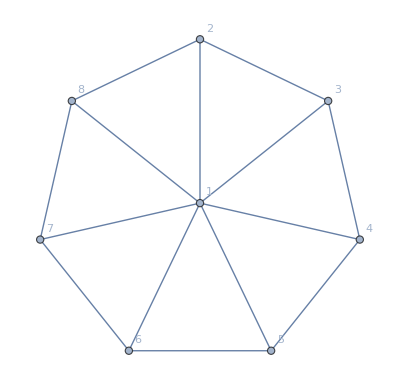

```mathematica
g//graphFromG
```

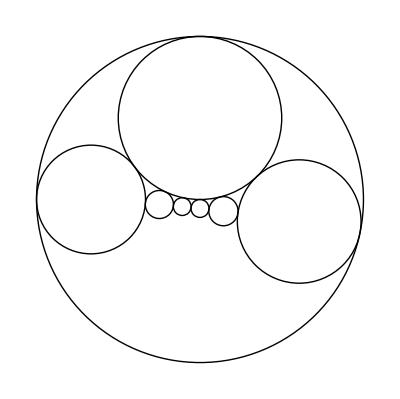

```mathematica
root=rootTupleFromG[g,"Face"->{1,2,3},"Invert"->5];
graphAbbc[root]
```

```mathematica
root
```

{{31.1836,20.1957,-16.1957,19.1957},{265.507,183.737,-147.346,164.541},{160.333,112.954,-88.9783,100.966},{35.6775,26.6896,-19.7995,23.6896},{-14.5918,-10.0978,8.09783,-9.09783},{47.3793,30.2935,-26.2935,27.2935},{174.925,117.448,-97.0762,105.46},{272.001,185.737,-150.949,166.541}}

```mathematica
alg=findGeneratorsFromG[N[g]]//Chop
```

{{{1.,0,0,0,0,0,0,0},{0,1.,0,0,0,0,0,0},{6.49396,5.04892,0,0,-0.356896,0,0,2.80194},{14.5918,9.09783,0,0,-0.801938,0,0,7.2959},{18.1957,10.0978,0,0,-1.,0,0,10.0978},{14.5918,7.2959,0,0,-0.801938,0,0,9.09783},{6.49396,2.80194,0,0,-0.356896,0,0,5.04892},{0,0,0,0,0,0,0,1.}},{{1.,0,0,0,0,0,0,0},{0,1.,0,0,0,0,0,0},{0,0,1.,0,0,0,0,0},{6.49396,3.24698,4.69202,0,0,0,-0.445042,0},{14.5918,8.2959,8.2959,0,0,0,-1.,0},{18.1957,11.3448,9.09783,0,0,0,-1.24698,0},{14.5918,10.0978,6.49396,0,0,0,-1.,0},{6.49396,5.49396,2.44504,0,0,0,-0.445042,0}},{{1.,0,0,0,0,0,0,0},{6.49396,-1.,6.49396,2.,0,0,0,0},{0,0,1.,0,0,0,0,0},{0,0,0,1.,0,0,0,0},{6.49396,-1.,4.24698,4.24698,0,0,0,0},{14.5918,-2.24698,10.5429,7.2959,0,0,0,0},{18.1957,-2.80194,14.1468,7.85086,0,0,0,0},{14.5918,-2.24698,12.3448,5.49396,0,0,0,0}},{{1.,0,0,0,0,0,0,0},{14.5918,0,0,8.2959,8.2959,0,-1.,0},{6.49396,0,0,4.69202,3.24698,0,-0.445042,0},{0,0,0,1.,0,0,0,0},{0,0,0,0,1.,0,0,0},{6.49396,0,0,2.44504,5.49396,0,-0.445042,0},{14.5918,0,0,6.49396,10.0978,0,-1.,0},{18.1957,0,0,9.09783,11.3448,0,-1.24698,0}},{{1.,0,0,0,0,0,0,0},{18.1957,0,0,0,9.09783,11.3448,0,-1.24698},{14.5918,0,0,0,8.2959,8.2959,0,-1.},{6.49396,0,0,0,4.69202,3.24698,0,-0.445042},{0,0,0,0,1.,0,0,0},{0,0,0,0,0,1.,0,0},{6.49396,0,0,0,2.44504,5.49396,0,-0.445042},{14.5918,0,0,0,6.49396,10.0978,0,-1.}},{{1.,0,0,0,0,0,0,0},{14.5918,0,0,-1.,0,8.2959,8.2959,0},{18.1957,0,0,-1.24698,0,11.3448,9.09783,0},{14.5918,0,0,-1.,0,10.0978,6.49396,0},{6.49396,0,0,-0.445042,0,5.49396,2.44504,0},{0,0,0,0,0,1.,0,0},{0,0,0,0,0,0,1.,0},{6.49396,0,0,-0.445042,0,3.24698,4.69202,0}},{{1.,0,0,0,0,0,0,0},{6.49396,0,0,-0.356896,0,0,2.80194,5.04892},{14.5918,0,0,-0.801938,0,0,7.2959,9.09783},{18.1957,0,0,-1.,0,0,10.0978,10.0978},{14.5918,0,0,-0.801938,0,0,9.09783,7.2959},{6.49396,0,0,-0.356896,0,0,5.04892,2.80194},{0,0,0,0,0,0,1.,0},{0,0,0,0,0,0,0,1.}},{{-1.,0.274127,0,-0.152129,0.34183,0,0,0},{0,1.,0,0,0,0,0,0},{0,0.445042,0,1.,-0.445042,0,0,0},{0,0,0,1.,0,0,0,0},{0,0,0,0,1.,0,0,0},{0,0.445042,0,-1.24698,1.80194,0,0,0},{0,1.,0,-1.80194,1.80194,0,0,0},{0,1.24698,0,-1.24698,1.,0,0,0}}}

```mathematica
FindFace[graphFromG[g]]-1
```

{{0,1,7},{0,2,1},{0,3,2},{0,4,3},{0,5,4},{0,6,5},{0,7,6},{1,2,3,4,5,6,7}}

```mathematica
root=rootTupleFromG[octahedron,"Exact"->True,"Invert"->5]
```

{{10,8,-4 √2,7},{24,24,-12 √2,17},{8,10,-4 √2,7},{12,10,-6 √2,7},{-4,-4,2 √2,-3},{10,12,-6 √2,7}}

```mathematica
alg=RootApproximant[findGeneratorsFromG[octahedron]];
```

```mathematica
geom=Transpose[root].Transpose[#].PseudoInverse[Transpose[root]]&/@alg//Simplify;
```

```mathematica
c=root[[-1]]
```

{10,12,-6 √2,7}

```mathematica
geom[[8]].c
```

{10,12,-6 √2,7}

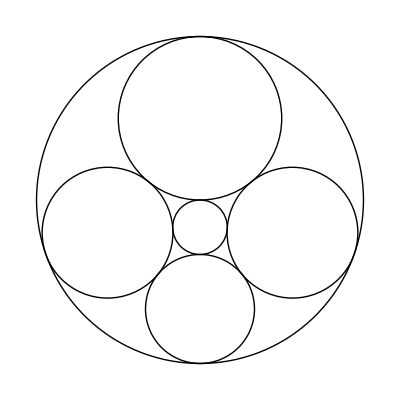

```mathematica
root//graphAbbc
```

```mathematica
root//N
```

{{10.,8.,-5.65685,7.},{24.,24.,-16.9706,17.},{8.,10.,-5.65685,7.},{12.,10.,-8.48528,7.},{-4.,-4.,2.82843,-3.},{10.,12.,-8.48528,7.}}

```mathematica
{{10.,8.,-5.656854249492381,7.},{24.,24.,-16.970562748477143,17.},{8.,10.,-5.656854249492381,7.},{12.,10.,-8.485281374238571,7.},{-4.,-4.,2.8284271247461903,-3.},{10.,12.,-8.485281374238571,7.}}
```